# Fit vertex angles in experiments, measure domain sizes, and the number of vertices (corners) of each domain

[MinD] = 2 µM
[MinE-His] = 8 µM

```mathematica
img=First@First@First@Import[ParentDirectory@ParentDirectory@ParentDirectory[NotebookDirectory[]]<>"/GlockEtAl-RawData/Glock et al. MinE-His Stationary patterns-snapshots/180427_ch1_2uM-MinD_8uM-E-His_snap01.lsm"];
```

```mathematica
img2=First@First@First@Import[ParentDirectory@ParentDirectory@ParentDirectory[NotebookDirectory[]]<>"/GlockEtAl-RawData/Glock et al. MinE-His Stationary patterns-snapshots/180427_ch1_2uM-MinD_8uM-E-His_snap02.lsm"];
```

```mathematica
img3=First@First@First@Import[ParentDirectory@ParentDirectory@ParentDirectory[NotebookDirectory[]]<>"/GlockEtAl-RawData/Glock et al. MinE-His Stationary patterns-snapshots/180427_ch1_2uM-MinD_8uM-E-His_snap03.lsm"];
```

Separate MinD and MinE channels

```mathematica
imgSep=ColorSeparate[img];
imgSep2=ColorSeparate[img2];
imgSep3=ColorSeparate[img3];
```

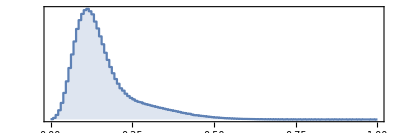
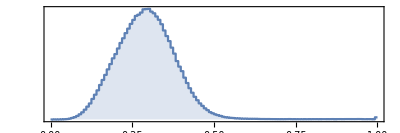

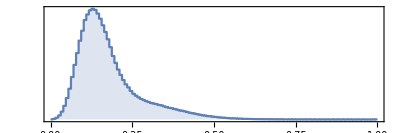
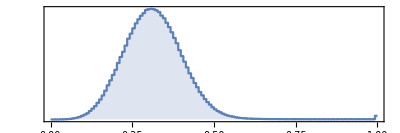

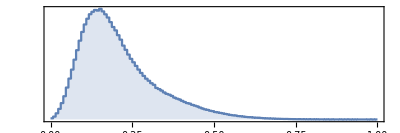
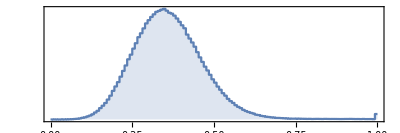

```mathematica
ImageHistogram/@ImageAdjust/@imgSep
ImageHistogram/@ImageAdjust/@imgSep2
ImageHistogram/@ImageAdjust/@imgSep3
```

```mathematica
imgReg={ImageAdjust[ImageAdjust@imgSep[[1]],0,{0,0.5}],ImageAdjust@imgSep[[2]]};
imgReg2={ImageAdjust[ImageAdjust@imgSep2[[1]],0,{0,0.5}],ImageAdjust@imgSep2[[2]]};
imgReg3={ImageAdjust[ImageAdjust@imgSep3[[1]],0,{0,0.6}],ImageAdjust@imgSep3[[2]]};
```

```mathematica
colorMap={minD,minE,minE+minD/1.5};
```

Image 1, (not shown)

```mathematica
imgColor=ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@imgReg))
```

Image 2, Extended Data Fig. 1b

```mathematica
imgColor2=ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@imgReg2))
```

Image 3, Extended Data Fig. 1b

```mathematica
imgColor3=ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@imgReg3))
```

## Image preparation

### MinD-MinE pixel clustering (using first image)

```mathematica
classImage=BrightnessEqualize[ImageAdjust[#]]&/@imgSep;
```

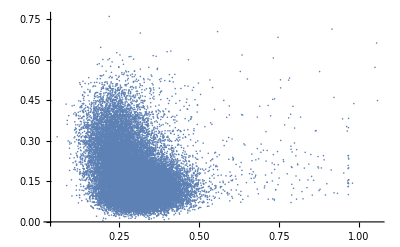

```mathematica
ListPlot[Transpose[Flatten/@{ImageData[classImage[[2]]],ImageData[classImage[[1]]]}[[All,;;200,;;200]]],PlotRange->All]
```

```mathematica
clusters=FindClusters[Transpose[Flatten/@{ImageData[classImage[[2]]],ImageData[classImage[[1]]]}],2,Method->"KMeans",DistanceFunction->EuclideanDistance];
```

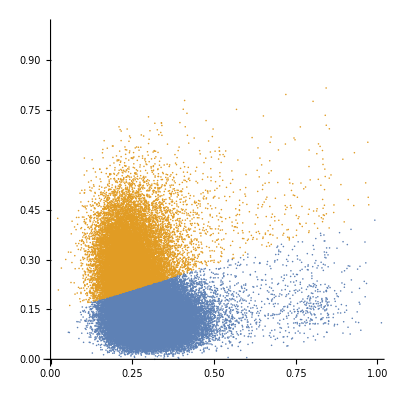

```mathematica
ListPlot[clusters[[All,;;;;10]],PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

```mathematica
centroids=Mean/@clusters;
```

```mathematica
ratioDE=#[[1]]/#[[2]]&@First@Differences[centroids]
```

-0.301736

### Mesh binarization

```mathematica
ClearAll@meshBinarize;
Options[meshBinarize]={"ThresholdPixelNumber"->10};
meshBinarize[img_,ratioDE_,opts:OptionsPattern[]]:=Block[
{imgEq=BrightnessEqualize[ImageAdjust[#]]&/@img,
minDMeas,
minE,
minD,
imgProj,
imgBinarized,
morphImg,
smallComponents,
morphMask,
imgBinarizedCleaned
},
minDMeas=ImageMeasurements[imgEq[[2]],{"Mean","StandardDeviation"}];
minE=imgEq[[1]];
(*to ignore MinD aggregates, cut brightness at mean+std off*)
minD=ImageClip[imgEq[[2]],{0,Total@minDMeas}];
(*project pixel MinD MinE fluorescence values on the axis connecting the centroids of the clusters identified in the initial image*)
imgProj=Image[ImageData[minE]+ratioDE ImageData[minD]];
(*binarize along this axis, and smooth to get a connected mesh*)
imgBinarized=Binarize[GaussianFilter[Binarize[ImageAdjust@imgProj],5],0.3];

(*remove too small morphological components*)
morphImg=MorphologicalComponents[imgBinarized];
smallComponents=Keys@Select[ComponentMeasurements[morphImg,"Area"],#[[2]]<10&];
morphMask=Clip[morphImg/.Thread[smallComponents->-1],{-1,0}];
imgBinarizedCleaned=Image[ImageData[imgBinarized]+morphMask];

{imgProj,imgBinarizedCleaned}
]
```

```mathematica
imgProj=meshBinarize[imgSep,ratioDE];
```

```mathematica
imgProj2=meshBinarize[imgSep2,ratioDE];
```

```mathematica
imgProj3=meshBinarize[imgSep3,ratioDE];
```

Skeleton of the network

```mathematica
branchIm=Thinning[imgProj[[2]]]
```

-Graphics-

```mathematica
branchIm2=Thinning[imgProj2[[2]]];
branchIm3=Thinning[imgProj3[[2]]];
```

## Analysis

### Measurement functions

Fit the vertex by assuming Gaussian cross-sections of the vertex arms:

```mathematica
ClearAll@lossF;
lossF[vertexData_,x1_?NumericQ,x2_?NumericQ,angles_?VectorQ]:=
Total[
Function[d,
(d[[3]]-Exp[-#/((width/2)^2/Log[2])])^2&@Min[If[Length@#==0,{1000},#]&@((Norm[d[[{1,2}]]-{x1,x2}]^2-((d[[{1,2}]]-{x1,x2}).{Cos[#],Sin[#]})^2)&/@
Select[angles,
Function[angle,((d[[{1,2}]]-{x1,x2}).{Cos[angle],Sin[angle]})>-10^-10]
])
]]/@vertexData[[2]]];
```

```mathematica
ClearAll@measureData;
measureData[vertexData_,armNumber_]:=
Block[
{
dataW,
iniCond,
iniCondClean,
vars,
sol,sol2,
fitSuccess=1,
fit
},
(*get initial conditions for the angles of the vertex arms by making a radial histogram and finding its peaks*)
dataW=WeightedData[#[[All,1]],#[[All,2]]]&@({PlanarAngle[{0,0}->{{1,0},#[[{1,2}]]}],#[[3]]}&/@Transpose[{vertexData[[2,All,1]],vertexData[[2,All,2]],Rescale@vertexData[[2,All,3]]}]);
iniCond=If[#[[1]]>Pi,{#[[1]]-2Pi,#[[2]]},#]&/@({0.05+(HistogramList[dataW,{0,2Pi,0.2}][[1,#[[1]]]]),#[[2]]}&/@(FindPeaks[Last@HistogramList[dataW,{0,2Pi,0.2}],1,0,0,Padding->"Periodic"]));
(*take mean of peaks that lie close together; map angles onto [-Pi,Pi] range*)
iniCondClean=If[#>Pi,#-2Pi,If[#<-Pi,#+2Pi,#]]&/@
SortBy[DeleteDuplicates@Table[
Mean[
Select[Join[iniCond,{#[[1]]-2Pi,#[[2]]}&/@iniCond,{#[[1]]+2Pi,#[[2]]}&/@iniCond],Min[Abs[#[[1]]-ini[[1]]]<0.5&]]
],{ini,iniCond}],#[[2]]&][[All,1]];
If[Length[iniCondClean]<3,
sol=I,
iniCond=iniCondClean[[-armNumber;;]];
vars=Symbol["a"<>ToString[#]]&/@Range[Length@iniCond];
Quiet@Check[sol=Last@FindMinimum[lossF[vertexData,x1,x2,vars],Join[{{x1,0,-10,10},{x2,0,-10,10}},{vars[[#]],iniCond[[#]],-2Pi,2Pi}&/@Range[Length@iniCond]],AccuracyGoal->2,PrecisionGoal->2];,fitSuccess=0;];
(*Try a second time if it failed*)
If[fitSuccess==0,
sol2=Check[Last@FindMinimum[lossF[vertexData,x1,x2,vars],Join[{{x1,0,-10,10},{x2,0,-10,10}},{vars[[#]],iniCond[[#]],-2Pi,2Pi}&/@Range[Length@iniCond]],AccuracyGoal->2,PrecisionGoal->2,Method->"PrincipalAxis"],I];
sol=sol2;
];
];
If[sol===I,
I,
fit=Join[{vertexData[[1,1]]+x1,vertexData[[1,2]]+x2}/.sol,Sort[If[#<-Pi,#+2Pi,If[#>Pi,#-2Pi,#]]&/@(vars/.sol)]];
If[Min[Abs@Differences[fit[[2;;]]]]<0.01,
I,
fit]
]
];
```

## Determine branch points

The branch width is about 5 pixels, see below.
We prun branches shorter than 10 pixels because for their vertices no reliable angles can be determined (repeatedly to account for short, branched segments that we want to remove).

```mathematica
branchImPrun=Thinning[Pruning[Pruning[Pruning[branchIm,10],10],10]]
```

-Graphics-

```mathematica
branchPoints=MorphologicalBranchPoints[Binarize@branchImPrun];
```

```mathematica
branchPointCoords=ImageValuePositions[branchPoints,1];
```

```mathematica
HighlightImage[branchImPrun,{AbsolutePointSize[3],branchPointCoords}]
```

-Graphics-

```mathematica
branchImPrun2=Thinning[Pruning[Pruning[Pruning[branchIm2,10],10],10]];
branchPoints2=MorphologicalBranchPoints[Binarize@branchImPrun2];
branchPointCoords2=ImageValuePositions[branchPoints2,1];
```

```mathematica
branchImPrun3=Thinning[Pruning[Pruning[Pruning[branchIm3,10],10],10]];
branchPoints3=MorphologicalBranchPoints[Binarize@branchImPrun3];
branchPointCoords3=ImageValuePositions[branchPoints3,1];
```

Determine average branch width by binarizing the experimental network image (imgProj[[1]]) at half-maximum intensity, count the white pixels (width*length of network) and divide by the white pixels in the network skeleton (length of network because everywhere only one pixel wide)

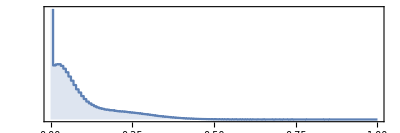

```mathematica
ImageHistogram[imgProj[[1]]]
```

Set 0.3 as branch intensity maximum and 0 as intensity minimum (intensity of plateaus)

```mathematica
width=N@Total@Flatten@ImageData[Binarize[ImageAdjust[imgProj[[1]],0,{0,0.3}],0.5]]/(Total@Flatten@ImageData@branchIm)
```

5.47123

## Vertices - Image 1

### Triple vertices

We define triple vertices as those branch points determined that are more than 10 pixels distant from other branch points (4-arm vertices are decomposed into two triple vertices in the network skeleton).

```mathematica
tripleVerticesRaw=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@branchPointCoords,0.]]}]/@branchPointCoords,#[[-1]]>10&];
Length@tripleVerticesRaw
```

566

So far, we got rid off 3-fold vertices that lie close by as we interpret those as 4-fold vertices that are decomposed in the skeleton network. However, there are also 4-fold vertices that remain as such in the skeleton network. We now identify those by counting the number of white pixels in the 3x3 neighborhood of a branch point. Triple vertices have 4 (one center + 3 arms), 4-fold vertices have 5 white pixels in this region .

```mathematica
tripleVertices=Block[{
tvs=tripleVerticesRaw,
branches=branchImPrun,
verticesImg,
verticesMorph,
quadVerts
},
verticesImg=ImageMultiply[ImageReflect@Dilation[Image[Transpose@SparseArray[Thread[Round[(tvs[[All,1]]+0.5)]->1],{1000,1000}]],ConstantArray[1,{3,3}]],branches];
verticesMorph=MorphologicalComponents[verticesImg];
quadVerts=Keys@Select[ComponentMeasurements[verticesMorph,"Count"],Values[#]>4&];

If[Length[quadVerts]>0,
verticesMorph=Binarize@ColorNegate@Image@Clip[verticesMorph/.Thread[quadVerts->-1],{-1,0}];
quadVerts=ImageValuePositions[MorphologicalBranchPoints[verticesMorph],1];

Select[tvs,Min[Function[x,Norm[x-#[[1]]]]/@quadVerts]>0.1&],
tvs
]
];
```

```mathematica
Length@tripleVertices
```

566

### 4-fold vertices

```mathematica
quadrupleVerticesRaw=Complement[branchPointCoords,tripleVertices[[All,1]]];
quadrupleVertices=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@quadrupleVerticesRaw[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@quadrupleVerticesRaw],I];
Length@quadrupleVertices
```

33

```mathematica
vertices=Join[tripleVertices,quadrupleVertices];
```

```mathematica
HighlightImage[branchIm,{AbsolutePointSize[3],tripleVertices,AbsolutePointSize[6],quadrupleVertices}]
```

-Graphics-

## Analysis of triple vertices - Image 1

Experimental network data labeled by pixel positions

```mathematica
dataraw=ImageData[imgProj[[1]]];
```

```mathematica
{dy,dx}=Dimensions@dataraw;
```

```mathematica
data=Table[{j-0.5,dy-i+0.5,dataraw[[i,j]]},{i,1,Dimensions[dataraw][[1]]},{j,1,Dimensions[dataraw][[2]]}];
```

### Analysis

The fit data for each vertex is taken as the data points within a 20 pixel large radius around the branch point. If a second branch point lies closer than 20 pixels, the radius is reduced to this distance.

```mathematica
vertex3Data=Table[{vertex[[1]],{#[[1]]-vertex[[1,1]],#[[2]]-vertex[[1,2]],#[[3]]}&/@Select[Flatten[data[[Max[1,Floor[dy-vertex[[1,2]]-25]];;Min[dy,Ceiling[dy-vertex[[1,2]]+25]],Max[1,Floor[vertex[[1,1]]-25]];;Min[dx,Ceiling[vertex[[1,1]]+25]]]],1],Norm[vertex[[1]]-#[[{1,2}]]]<Min[20,vertex[[2]]]&]},{vertex,tripleVertices}];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[vertex3Data[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Disk[{0,0},1]]
],{i,1,Length@vertex3Data}]
```

Fit triple vertices and exclude those for which the fit does not converge.

```mathematica
vertex3MeasurementsRaw=ParallelTable[measureData[data,3],{data,vertex3Data},Method->"FinestGrained"];
```

FindMinimum::regex: Reached the point {16.1803,0.,-1.03319,1.05,0.05}, which is outside the region {{-10.,-10.,-6.28319,-6.28319,-6.28319},{10.,10.,6.28319,6.28319,6.28319}}.

```mathematica
fittedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw],ListQ[#[[2]]]&][[All,1]];
failedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw],#[[2]]==I&][[All,1]];
vertex3Measurements=DeleteCases[vertex3MeasurementsRaw,I];
Length[vertex3Data]
Length[vertex3Measurements]
```

0

564

```mathematica
failedVertices
```

{55,356}

```mathematica
Show[
ListDensityPlot[vertex3Data[[#,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Annulus[{0,0},{20,40}]]
]&/@failedVertices
```

{-Graphics-,-Graphics-}

```mathematica
Manipulate[
Show[
ListDensityPlot[(vertex3Data[[fittedVertices]])[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Join[{Annulus[{0,0},{20,40}],
Disk[vertex3Measurements[[Floor@i,;;2]]-(tripleVertices[[fittedVertices]])[[Floor@i,1]],1]},
{Darker@Red,Thick},
Flatten[Function[p,Line[{{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]],{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]]+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]@vertex3Measurements[[Floor@i]],1]]]
],{i,1,Length@vertex3Measurements}]
```

```mathematica
Show[
HighlightImage[imgProj[[1]],{AbsolutePointSize[5],tripleVertices}],
Graphics[Join[{Darker@Red,Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements,1],
{RGBColor[{255,150,20}/255]},
Circle[#,3]&/@quadrupleVertices]]
]
```

-Graphics-

```mathematica
angles3=(Join[#,{360-Total@#}]&@(180/Pi*Differences[#]))&/@(vertex3Measurements[[All,3;;]]);
```

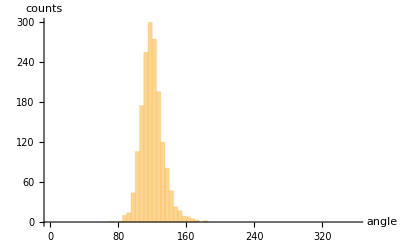

```mathematica
Histogram[{
Flatten[angles3,1]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[angles3,1]]
```

120.

```mathematica
StandardDeviation[Flatten[angles3,1]]
```

13.1202

#### FitList

```mathematica
vertex3MeasurementsRaw
```

{{531.512,985.516,-1.30906,0.949366,2.98305},{936.488,984.514,-2.08358,0.515971,2.04691},{447.498,983.502,-2.22533,0.127284,1.98689},{385.504,982.5,-2.14104,-0.453941,1.36103},{482.473,982.496,-1.65629,0.374324,2.49985},{673.498,982.508,-1.77192,0.553596,2.46234},{89.5085,981.51,-2.82073,-0.655671,1.37905},{760.497,981.496,-1.42501,0.721561,2.98146},{132.508,980.491,-2.75379,-0.34833,1.4634},{334.501,978.501,-1.98654,0.423609,2.21822},{815.837,971.237,-1.78801,0.537363,2.25319},{104.502,969.5,-1.63349,0.409166,2.46147},{53.5014,968.502,-1.62973,0.45171,2.61638},{195.522,963.522,-0.936603,0.814806,2.84327},{252.5,960.494,-2.5604,-0.544655,1.65865},{419.502,960.508,-1.45446,0.513075,2.45861},{872.516,960.498,-2.42887,-0.749923,1.66098},{304.502,959.495,-2.47393,-0.0800949,2.02713},{812.502,959.531,-2.81338,-0.734695,1.23585},{325.499,958.498,-0.85736,1.15867,3.10721},{612.498,958.498,-2.42079,-0.255797,1.7774},{533.523,957.498,-3.00454,-1.10506,1.42448},{52.5001,953.501,-2.61058,-0.509016,1.48703},{483.496,953.473,-2.2729,-0.0850974,1.8996},{663.508,952.498,-1.02377,1.09324,3.11978},{636.499,949.506,-1.61668,0.258282,2.6812},{370.502,947.496,-3.03901,-0.876149,1.23407},{886.497,947.53,-1.62073,0.375844,2.36338},{764.501,946.499,-2.35766,-0.300305,1.76707},{275.489,943.51,-1.9114,0.368567,2.39938},{475.511,943.997,-1.12209,0.886586,3.06711},{339.505,941.513,-1.90075,0.269488,2.19793},{215.506,940.499,-1.36414,0.437919,2.37379},{784.502,940.516,-1.10705,0.861386,2.89603},{153.512,936.507,-2.72635,-0.805629,1.09457},{833.5,935.505,-1.71591,0.486599,2.23483},{25.4971,934.5,-1.45415,0.62036,2.49192},{886.487,933.481,-2.45915,-0.47839,1.59989},{542.497,926.502,-2.6924,-0.63906,1.69339},{742.515,922.506,-0.977218,0.8598,2.99615},{939.521,922.516,-1.15776,0.802333,3.04292},{418.498,921.499,-2.82216,-0.614584,1.32114},{906.506,921.521,-1.87007,0.173741,2.56051},{594.526,919.493,-2.90006,-0.744733,1.46599},{485.16,919.17,-2.17277,-0.0264034,1.96838},{121.741,916.987,-1.64229,0.368488,2.4566},{218.199,916.877,-3.13,-1.58187,1.59712},{337.493,916.497,-2.22874,-0.229,1.69171},{400.486,916.509,-2.06392,0.200688,2.30446},{172.498,914.5,-2.05408,0.0470949,2.24146},{558.493,913.491,-1.96853,0.0944244,2.40719},{686.502,913.516,-1.99516,0.145861,2.21268},{713.719,913.765,-1.30011,0.738103,3.01029},{269.501,910.496,-2.50891,-0.535883,1.53056},ⅈ,{639.502,901.472,-2.89937,-0.479859,1.47266},{613.489,897.498,-2.16834,0.0392764,2.17935},{949.487,897.493,-2.39952,-0.462691,1.94448},{855.508,896.51,-2.73928,-0.723976,1.06482},{465.493,895.499,-1.2828,0.759274,2.48898},{755.619,893.099,-2.60721,-0.884075,1.7828},{80.807,889.194,-2.71185,0.511324,1.9864},{330.481,889.692,-2.95247,-0.931282,1.54585},{979.84,886.773,-1.32389,0.918869,2.91312},{39.4951,884.47,-2.30624,-0.142658,2.0778},{297.5,884.496,-1.94496,-0.00197173,2.12321},{378.501,884.502,-3.07948,-0.861238,0.933949},{336.436,882.044,-2.05208,0.0962816,2.18065},{134.493,880.506,-2.11482,0.0242491,2.22383},{152.506,880.505,-0.969994,0.963533,3.09808},{470.493,879.495,-2.42229,-0.580476,1.83959},{598.519,875.499,-1.48296,0.968731,2.75842},{30.6586,875.033,-1.22365,0.836744,2.78584},{124.517,864.496,-1.30963,1.06765,3.13351},{330.506,862.502,-2.59288,-0.524797,1.30294},{402.506,862.516,-1.42657,0.560257,2.55997},{773.542,864.383,-2.11284,-0.0884402,2.02595},{983.51,860.5,-2.78654,-0.864152,1.61767},{552.489,859.485,-2.70548,-0.492111,1.58191},{270.499,858.511,-1.41227,0.575817,2.74242},{215.51,855.494,-1.48719,0.755225,2.7694},{595.439,848.395,-3.04757,-0.725502,1.26338},{662.5,848.504,-2.62115,-0.560153,1.49772},{892.493,846.468,-2.27045,-0.0564517,2.12945},{514.494,844.496,-1.97202,0.415145,2.37465},{403.505,841.501,-2.64756,-0.56091,1.48381},{215.523,835.488,-2.76889,-0.67179,1.47454},{449.499,835.499,-2.64644,-0.621668,1.48051},{79.4984,834.494,-2.78626,-0.650364,1.29798},{127.498,834.487,-2.60727,-0.506442,1.53574},{756.245,832.566,-1.5068,1.04385,2.59449},{167.821,828.081,-2.9332,-0.465867,1.56834},{694.502,829.501,-1.44806,0.65064,2.63622},{60.4748,827.5,-1.57361,0.347294,2.07613},{372.505,827.504,-1.87549,0.349237,2.42829},{143.502,825.497,-1.7913,0.00974487,2.64964},{613.511,825.494,-2.25894,-0.112369,2.05111},{431.501,824.516,-1.53792,0.591845,2.54896},{635.504,824.493,-3.10788,-0.82956,0.957562},{280.484,823.472,-2.44377,-0.196108,1.96196},{293.775,821.543,-1.07322,0.936103,3.01173},{181.509,820.512,-1.38991,0.678129,2.59781},{99.4958,819.499,-1.79419,0.471346,2.53356},{884.503,818.497,-2.62781,-0.621501,1.74927},{963.511,810.515,-1.50748,0.554595,2.59677},{866.501,808.502,-1.75433,0.479253,2.36957},{430.676,807.161,-2.94303,-1.03095,1.47333},{812.5,807.494,-2.18364,-0.469076,2.19993},{257.503,806.513,-1.59239,0.555639,2.60798},{320.51,802.507,-1.06574,0.928597,2.99739},{184.502,799.498,-2.57592,-0.633159,1.67574},{697.492,798.499,-2.6143,-0.529945,1.62619},{755.496,793.496,-2.87905,-0.664777,1.29769},{585.504,791.501,-1.40643,0.645556,2.44784},{57.4967,790.486,-2.40606,-0.341379,1.46324},{859.528,787.47,-3.06513,-1.14117,1.09584},{84.5197,785.5,-0.917363,0.958122,3.10177},{329.498,785.506,-2.37756,-0.530375,1.98516},{672.484,784.502,-1.68577,0.511563,2.38474},{794.509,784.492,-3.01734,-0.814399,0.870625},{733.5,782.504,-1.44564,0.648715,2.71303},{441.494,781.489,-2.438,-0.0765849,1.90279},{538.495,781.494,-2.44063,-0.42889,2.06866},{465.506,780.494,-3.13426,-0.838724,1.01827},{971.498,780.479,-2.14119,-0.0938777,2.04984},{210.497,777.51,-1.50992,0.582935,2.39877},{865.512,772.519,-2.73472,-0.857948,1.91198},{32.5135,770.506,-1.33529,0.649519,2.70154},{587.504,770.491,-2.5742,-0.626873,1.55318},{98.4925,766.486,-2.11776,-0.031141,2.1658},{306.494,764.497,-2.90314,-1.05481,0.732169},{479.506,764.507,-1.90665,-0.120689,2.22813},{572.501,761.5,-1.63768,0.48439,2.50595},{815.501,760.494,-2.17789,-0.00871488,2.24388},{876.472,760.493,-1.86991,0.121766,2.24797},{141.505,757.499,-1.19902,0.675048,2.77625},{667.516,757.499,-2.64218,-0.790561,1.34145},{509.5,756.499,-1.43103,0.709198,2.75256},{958.169,754.095,-2.83779,-0.758876,1.21816},{265.474,751.511,-1.98596,0.286922,2.14953},{407.518,751.499,-0.908938,0.91349,2.91416},{944.503,748.514,-1.84641,0.437871,2.31867},{213.484,747.495,-2.69521,-0.436163,1.64911},{620.491,742.496,-2.08241,-0.0756713,2.35011},{197.485,739.509,-2.04045,0.43019,2.3606},{639.615,740.308,-1.43424,0.624089,2.96463},{259.515,735.494,-2.87116,-0.770824,1.33219},{421.182,733.99,-1.91992,-0.163652,2.20692},{244.484,729.517,-1.75427,0.424136,2.4685},{461.507,729.497,-3.05046,-0.842643,1.02293},{732.512,727.499,-2.67869,-0.581932,1.2507},{33.5046,725.652,-2.87469,-0.502156,1.47241},{515.503,726.504,-2.40982,-0.341633,1.80839},{716.568,720.053,-1.72678,0.383017,2.52183},{881.489,719.499,-2.43296,-0.37786,1.93727},{290.505,718.496,-0.854595,0.653512,3.02641},{561.509,715.496,-3.12974,-0.812947,1.16645},{345.501,713.502,-2.54942,-0.59432,1.45925},{74.5043,707.496,-1.4462,0.84984,2.77039},{239.164,707.48,-1.64449,1.26708,3.01212},{905.506,707.547,-1.83386,0.177661,2.58036},{484.493,705.491,-1.93152,0.425245,2.38254},{161.518,703.486,-2.5169,-0.100532,1.82489},{780.516,702.47,-1.11503,1.052,2.81683},{175.067,701.806,-1.03009,0.780158,2.97166},{415.491,700.502,-2.56466,-0.532517,1.59765},{712.504,697.493,-2.5115,-0.600696,1.3823},{151.528,696.471,-1.34988,0.51107,2.77317},{313.499,693.5,-1.64049,0.484229,2.34355},{596.652,689.928,-2.95773,-1.01777,1.37288},{582.448,688.075,-2.23926,0.154137,2.12031},{391.519,685.517,-1.48006,0.550914,2.64084},{81.5089,684.529,-2.18308,-0.009017,2.10492},{92.701,683.942,-1.15762,0.676092,3.00194},{967.5,678.507,-3.02324,-1.02856,0.759456},{689.503,677.523,-3.07002,-0.782736,0.812976},{790.494,677.501,-2.17548,-0.1754,1.84945},{311.864,675.56,-2.9112,-0.689791,1.43056},{472.504,674.509,-2.67127,-0.738432,1.18393},{814.5,674.493,-0.862499,1.10814,3.12269},{289.497,671.504,-2.43794,0.12544,2.29896},{841.497,670.514,-2.71563,-0.515579,1.46755},{610.497,669.512,-1.84548,0.156212,2.20022},{218.501,666.508,-1.44944,0.801512,2.72015},{451.502,662.503,-1.99133,0.548824,2.31687},{824.509,662.504,-1.5597,0.472524,2.23055},{775.921,653.966,-2.63256,-0.612305,1.04802},{152.513,650.503,-2.63135,-0.667585,1.49974},{37.4666,649.424,-2.23906,-0.31401,1.97664},{49.7749,645.206,-1.32957,0.599638,2.79605},{503.515,641.495,-1.49753,0.603788,2.52551},{550.512,641.502,-1.34834,0.85803,2.66638},{219.51,639.509,-2.79319,-0.329466,1.44013},{132.509,638.508,-1.49179,0.571066,2.55156},{652.511,637.499,-2.56492,-0.635503,1.44518},{753.502,634.507,-0.860691,0.924559,3.11442},{233.758,634.52,-1.30387,0.591246,2.78758},{735.561,634.416,-1.93091,0.0771781,2.19792},{385.508,631.5,-2.88985,-0.743094,1.29522},{202.954,632.211,-1.60552,0.448515,2.96179},{53.5025,628.485,-2.50677,-0.746383,1.81881},{345.488,625.499,-2.613,0.053728,1.98228},{821.509,622.503,-2.66766,-0.74019,1.46048},{399.483,618.495,-1.70356,0.411157,2.38074},{553.515,618.5,-2.74854,-0.963306,1.59727},{917.495,614.507,-2.25623,-0.117532,2.111},{132.503,607.502,-2.61387,-0.550033,1.50729},{503.496,604.494,-2.65952,-0.491726,1.54254},{680.491,604.5,-2.04294,-0.172138,2.14692},{783.505,604.509,-1.59122,0.503053,2.52413},{960.517,604.51,-1.35781,0.651018,2.74346},{246.489,602.502,-2.07512,0.0779738,1.95236},{842.501,599.497,-2.13052,0.0704455,2.22324},{567.492,596.498,-2.01173,-0.222328,2.08724},{712.501,595.517,-1.05283,0.739319,2.74198},{67.5066,594.502,-2.66445,-0.795469,1.44393},{310.511,591.52,-0.936184,0.906524,2.78725},{401.501,590.5,-2.35047,-0.298223,1.84546},{179.509,589.5,-3.12334,-0.925905,0.876025},{617.498,587.513,-2.7555,-0.636631,1.18189},{419.52,585.493,-0.853048,0.955226,2.91652},{100.511,584.507,-3.04947,-0.939175,0.780155},{79.4974,581.516,-1.85545,0.175093,2.29336},{831.864,581.367,-3.04549,-1.16364,1.06675},{965.924,581.636,-1.8675,-0.0655906,1.79348},{602.488,580.502,-1.70682,0.45321,2.51749},{471.506,577.5,-1.22681,1.08875,2.89867},{227.159,574.532,-3.00625,-1.14683,1.06627},{355.494,573.498,-2.38373,-0.422093,1.47813},{429.511,573.518,-1.71708,0.372985,2.21382},{547.506,573.5,-1.68945,0.498339,2.50464},{195.498,569.509,-1.96731,0.143428,2.25491},{733.483,568.51,-2.01165,0.400191,2.39439},{326.494,567.496,-2.39277,-0.423452,2.09511},{647.177,568.168,-1.55278,0.623903,2.71136},{29.5129,564.505,-3.0294,-1.11706,1.18017},{377.499,564.502,-1.37152,0.818861,2.7726},{232.114,561.848,-2.38326,-0.524767,1.89144},{836.499,561.499,-2.42815,-0.563531,1.67671},{923.498,561.506,-1.55043,0.69856,2.47992},{341.514,560.512,-1.17948,0.728296,2.69299},{76.487,558.5,-2.38329,-0.335665,1.56469},{188.515,555.493,-3.10132,-1.02511,1.13183},{599.496,549.496,-2.59079,-0.578154,1.54796},{865.517,547.509,-1.07645,0.747695,2.74538},{425.232,546.154,-2.95407,-1.03369,1.39759},{34.2337,542.719,-2.88701,-1.05412,1.54134},{720.516,542.497,-2.95065,-0.930221,1.06151},{252.482,541.486,-2.23042,-0.150553,2.17457},{126.491,540.49,-2.33462,-0.636299,2.15527},{383.808,539.862,-1.64459,0.0630561,1.87004},{640.457,534.869,-1.12224,1.12282,2.9997},{922.548,533.525,-2.88735,-0.910052,1.40728},{201.507,530.502,-2.45818,-0.945492,2.01734},{488.5,528.497,-2.61346,-0.581578,1.69872},{960.505,528.479,-2.72326,-0.643864,1.36641},{303.506,527.518,-3.11641,-0.987306,1.13011},{112.502,525.521,-3.13055,-1.12849,0.847492},{45.4914,522.489,-2.34151,-0.542281,2.07476},{280.496,522.503,-1.86002,0.412834,2.23425},{880.465,522.496,-1.65719,0.248614,2.18467},{932.482,521.495,-1.95491,0.0674944,2.13824},{185.507,517.505,-1.57961,0.666891,2.63436},{438.499,517.483,-2.33448,-0.0667399,1.92467},{234.506,513.498,-3.03386,-0.719799,1.07755},{65.4993,510.506,-1.7949,0.484633,2.60556},{513.492,508.502,-1.70285,0.425769,2.32191},{741.492,507.503,-2.25014,-0.291228,2.1182},{510.955,495.629,-3.05921,-1.02753,1.33048},{256.509,494.496,-1.68684,0.401473,2.45663},{421.156,494.704,-3.10311,-0.921589,1.03099},{564.501,494.5,-2.35616,-0.375699,2.03692},{692.494,493.499,-3.03643,-0.627381,1.14493},{667.487,492.483,-2.13918,-0.0393345,2.15787},{328.487,491.514,-1.61902,0.215739,2.3241},{925.126,491.182,-3.02938,-0.913009,1.33651},{811.435,491.064,-2.04491,0.097345,2.18938},{855.517,482.525,-1.87266,0.204027,2.56615},{713.433,479.709,-1.73611,0.665504,2.61182},{432.497,478.5,-2.37497,-0.517485,2.16186},{188.487,476.501,-2.18951,-0.292833,1.85137},{522.49,475.5,-2.00726,0.046873,2.12467},{974.537,475.508,-3.13982,-0.68406,1.25028},{55.5122,473.498,-2.81386,-0.736816,1.3022},{327.512,465.51,-2.70556,-0.966595,1.56846},{454.452,466.526,-1.62572,0.440036,2.64898},{12.4874,460.509,-1.39773,0.385072,2.01902},{642.496,456.497,-0.953222,0.863779,2.36616},{264.497,454.499,-2.24737,-0.247129,2.0538},{692.51,451.504,-1.38646,0.592938,2.58161},{176.45,448.203,-2.7432,-0.649995,1.36805},{414.292,445.741,-2.89095,-0.602948,1.26482},{292.51,445.505,-1.4942,0.709421,2.75412},{603.489,445.502,-1.91617,0.134406,2.07479},{163.486,442.512,-1.68741,0.439273,2.57927},{401.489,442.527,-2.03016,0.254141,2.2968},{17.5006,440.485,-2.28456,-0.465828,1.86686},{523.497,439.493,-2.00569,-0.0393756,2.06488},{545.503,438.507,-0.757164,0.89834,3.08093},{819.483,437.488,-2.00764,-0.043816,1.94138},{772.493,434.499,-2.59339,-0.904888,1.32211},{696.489,432.495,-2.56548,-0.347574,1.79505},{654.507,431.503,-2.63658,-0.590703,1.83945},{874.684,429.263,-2.87124,-0.742221,1.37459},{204.503,427.516,-1.67474,0.11849,2.47881},{230.5,425.504,-1.4365,0.753241,2.85275},{860.028,425.297,-1.90282,0.269013,2.49658},{49.8113,424.003,-1.78388,0.734751,2.65493},{753.511,421.505,-1.36548,0.648301,2.67842},{959.501,419.509,-2.17971,-0.275519,1.99991},{673.412,418.554,-1.52995,0.524883,2.53112},{989.214,416.127,-3.11954,-0.420471,1.5004},{598.467,414.484,-2.38303,-0.480043,1.65872},{348.496,412.499,-2.2017,-0.186929,2.26848},{513.494,409.45,-2.85724,-0.56649,1.40376},{804.522,409.491,-1.19022,0.986446,2.94697},{500.924,407.31,-2.08767,0.0965565,2.14226},{156.506,405.505,-3.04144,-1.07906,1.37682},{618.503,404.507,-1.0129,0.740561,2.70922},{41.535,403.496,-0.92932,1.0111,3.13016},{135.506,402.506,-1.94057,0.152066,2.25304},{577.496,400.494,-2.47981,0.421272,2.13011},{675.49,397.495,-2.41794,-0.484401,1.70539},{305.482,393.495,-2.12662,-0.108668,2.12674},{421.504,393.5,-1.39952,0.670425,2.69887},{923.494,392.515,-1.6834,0.524722,2.60627},{331.512,390.505,-1.00809,0.884559,3.06057},{51.5007,387.498,-2.59002,-0.869131,2.00989},{166.508,385.507,-2.2481,-0.384616,2.00695},{545.501,385.501,-1.80705,0.239447,2.28713},{631.511,385.514,-1.95616,0.161802,2.20061},{810.866,382.653,-2.69107,-0.0813019,1.65513},{839.504,384.494,-2.96844,-0.80967,1.04096},{659.515,383.499,-1.49218,0.707324,2.80405},{383.496,378.492,-2.44301,-0.634835,1.38363},{230.506,377.498,-2.85546,-0.618048,1.4148},{764.492,375.504,-2.14971,-0.130067,1.9439},{260.476,373.493,-2.37819,-0.289919,1.71866},{293.505,373.5,-3.05406,-0.854693,1.10135},{919.508,371.509,-2.86075,-0.958546,1.35255},{22.4969,370.504,-1.64435,0.498258,2.64998},{116.524,370.516,-0.972799,0.885428,2.96688},{788.506,369.494,-1.43113,0.609912,2.78229},{191.499,368.514,-1.92081,0.191445,2.34905},{252.448,365.807,-1.45926,0.768857,2.75875},{537.512,365.491,-2.69512,-0.814051,1.12088},{75.5001,364.501,-1.82173,0.425803,2.47312},{610.964,365.815,-1.54456,0.450002,2.99007},{496.457,363.484,-2.49031,-0.457861,1.67018},{751.507,357.508,-3.12681,-1.01521,0.95667},{515.5,355.501,-1.38421,0.355611,2.77835},{713.496,354.481,-2.38711,-0.0635569,2.05435},{463.482,352.5,-1.5949,0.0158226,1.79824},{662.494,352.49,-1.76585,-0.0765952,1.69587},{886.511,350.506,-1.12614,0.734451,2.72349},ⅈ,{563.502,347.514,-1.14682,0.814065,2.72453},{130.489,346.532,-2.0445,0.247165,2.10771},{701.514,343.511,-1.41276,0.752633,2.73275},{58.5004,338.497,-1.60138,0.657819,2.53093},{331.512,336.499,-1.68395,0.493115,2.44628},{176.51,335.494,-1.03822,0.989455,3.07953},{426.509,334.493,-3.1305,-0.734803,1.15482},{938.494,333.487,-2.562,-0.00268777,2.05441},{251.51,332.503,-2.51404,-0.639541,1.54346},{13.5081,330.499,-2.77993,-0.777351,1.26437},{963.513,330.506,-1.16145,0.705725,2.92731},{756.502,322.506,-2.68532,-0.513038,1.36885},{892.502,321.497,-2.72061,-0.443762,1.50581},{657.51,317.5,-2.80171,-0.509356,1.46943},{853.491,316.501,-2.85201,-0.316343,1.64471},{584.503,314.499,-2.34411,-0.124093,2.20038},{909.515,314.516,-1.17922,0.83949,2.81146},{433.515,312.487,-2.78036,-0.971296,1.00035},{474.491,311.488,-2.23148,-0.085028,1.89093},{522.745,307.174,-2.5991,-0.102391,1.82302},{623.496,303.501,-1.8293,0.477266,2.66304},{40.4963,302.506,-0.988918,0.732507,2.32585},{569.513,300.51,-1.34847,0.716026,2.79414},{221.512,299.498,-2.65578,-0.798949,1.04149},{184.495,298.511,-2.4047,-0.54222,1.55156},{723.408,299.03,-1.2208,0.833,3.01497},{400.501,297.515,-1.59459,0.524063,2.53815},{122.51,296.493,-2.2833,-0.565155,1.75111},{504.5,296.502,-1.53345,0.522879,2.33143},{449.482,289.499,-1.6906,0.500465,2.17501},{50.51,287.53,-1.73516,0.267285,2.18568},{200.48,287.504,-1.18899,0.562312,2.43676},{321.477,286.496,-2.46657,-0.382787,1.61867},{920.505,286.505,-2.38458,-0.28032,1.98621},{292.497,284.495,-2.36382,-0.431575,2.03395},{106.498,281.502,-1.68572,0.674537,2.73757},{937.503,280.521,-1.83022,0.263614,2.75084},{156.498,278.509,-1.0101,0.55669,2.55164},{504.505,277.496,-2.72886,-0.724292,1.56834},{983.507,277.5,-1.55867,0.666893,2.763},{348.505,276.5,-0.852901,0.925088,2.82181},{309.482,276.499,-1.11747,0.719298,2.66322},{696.501,274.486,-2.34855,-0.426677,1.54321},{619.24,273.334,-2.42212,-0.514149,1.56694},{906.504,273.518,-1.25559,0.689104,2.81992},{729.513,272.499,-2.80122,-0.923,1.6731},{395.504,264.505,-2.65412,-0.558431,1.34152},{270.509,262.513,-3.13638,-0.996484,0.801073},{253.5,260.517,-1.88496,0.203662,2.31999},{317.497,260.494,-2.37634,-0.704557,2.09032},{680.512,259.502,-1.4862,0.704861,2.49818},{41.5013,258.501,-2.80845,-0.818215,1.14311},{448.503,258.499,-2.57006,-0.57573,1.61714},{171.508,254.494,-2.49701,-0.685951,2.12382},{475.513,254.487,-2.59057,-0.762463,1.09173},{96.5261,253.496,-1.08736,1.00114,2.9479},{376.494,253.514,-1.47607,0.539833,2.5387},{776.495,253.503,-2.10792,-0.283407,1.97577},{415.495,251.498,-1.94516,-0.0885406,2.55651},{981.501,249.499,-2.42596,-0.616982,1.44121},{464.485,247.498,-1.72813,0.545246,2.48231},{601.485,247.498,-2.26719,-0.491574,1.30179},{202.513,244.502,-3.04294,-0.966695,0.92947},{638.531,242.501,-2.9184,-0.670518,1.46182},{895.511,242.514,-1.30918,0.75091,2.8944},{541.443,239.489,-1.42876,0.726857,2.56064},{681.494,239.502,-2.46304,-0.401723,1.56306},{105.503,231.502,-2.42045,-0.357376,1.85183},{212.482,230.501,-2.12287,0.0533077,2.13688},{239.505,229.516,-0.79971,0.943714,2.99697},{303.521,227.503,-2.79506,-0.660421,1.43488},{542.505,227.516,-2.5169,-0.601878,1.66626},{951.499,227.508,-1.53685,0.565927,2.68055},{140.696,226.051,-1.04899,0.878956,3.08282},{657.488,224.519,-2.06535,0.208556,2.28111},{767.5,223.491,-2.51288,-0.649183,1.52512},{582.508,222.508,-3.06512,-0.936369,0.942236},{343.502,217.505,-2.4432,-0.381383,1.88092},{556.495,217.503,-1.81977,0.297635,2.49928},{252.489,216.503,-1.94773,0.28101,2.36605},{376.495,216.505,-2.73933,-0.416123,1.5069},{407.497,216.493,-2.74304,-0.88641,1.52503},{457.499,215.492,-2.55226,-0.644509,1.33456},{651.613,212.439,-2.98261,-0.838102,1.14183},{514.495,211.5,-2.55184,0.445835,1.98648},{725.506,211.502,-2.56116,-0.659044,1.97016},{149.499,210.486,-2.21205,-0.100505,2.04497},{17.4968,207.502,-0.871906,0.948936,2.97315},{331.54,207.513,-1.42584,0.655876,2.59131},{790.493,204.505,-1.88782,0.19369,2.42821},{193.657,202.717,-1.21342,0.946013,2.85537},{739.499,200.502,-1.54779,0.481794,2.48773},{601.49,198.509,-1.81408,0.346758,2.29559},{422.497,197.506,-2.03864,0.0809803,2.1962},{893.845,196.634,-1.39888,0.590159,2.19022},{333.022,194.762,-2.59521,-0.615592,1.69656},{487.496,194.509,-1.94237,0.522526,2.49844},{836.503,192.504,-0.827783,0.930264,2.85373},{197.577,191.449,-2.05325,-0.254581,1.93636},{951.497,190.503,-2.70061,-0.79641,1.48966},{36.4869,187.501,-1.89707,0.458748,2.40603},{239.506,185.499,-3.01749,-0.817297,1.085},{221.503,182.511,-1.75767,0.1771,2.68068},{596.505,180.495,-2.91898,-0.990044,1.33149},{671.806,177.973,-1.71826,0.38656,2.21916},{741.553,176.517,-2.98366,-1.34604,1.70086},{899.49,176.503,-2.09377,-0.11183,2.01891},{964.496,176.494,-2.02551,-0.107401,2.29491},{411.498,174.505,-2.83686,-0.797612,1.14139},{553.051,173.665,-1.93126,-0.0327504,1.64581},{982.499,173.511,-1.35381,0.769429,2.90003},{134.508,172.498,-2.63137,-0.569356,1.42236},{892.91,164.672,-2.93277,-1.04356,1.09285},{477.507,164.497,-2.92808,-0.827105,1.26966},{27.5331,162.485,-2.75664,-0.693295,1.2031},{97.4982,162.5,-2.23721,0.0552848,2.05253},{365.497,160.507,-1.9313,0.376262,2.3385},{875.161,161.222,-1.77352,0.245,2.12134},{265.489,159.491,-1.94645,0.0273759,2.38967},{292.512,158.503,-1.13175,0.857485,3.04821},{428.494,156.495,-2.03276,0.0313601,2.30751},{671.395,156.306,-1.70089,-0.0296842,1.70803},{176.506,151.506,-1.19736,0.895725,2.81427},{608.503,147.502,-2.86683,-0.708077,1.63828},{84.5079,146.494,-2.68507,-0.801819,0.896421},{871.831,146.384,-2.93242,-1.04312,1.33849},{357.505,143.492,-2.80823,-0.846081,1.0737},{495.5,143.5,-2.14703,-0.0402578,2.22883},{547.232,138.067,-2.81906,-0.555384,1.47252},{751.495,137.477,-2.37489,-0.0832339,2.06495},{776.501,137.494,-3.05651,-0.631729,1.27537},{415.516,134.49,-1.25374,0.980883,3.01622},{52.4878,133.515,-2.43726,0.373897,2.16893},{522.495,133.5,-2.06948,0.0908613,2.51506},{559.521,131.504,-1.28512,0.769939,2.69084},{372.478,127.505,-1.82614,0.200728,2.3395},{262.51,126.502,-2.50331,-0.73709,1.75455},{311.5,126.505,-2.00206,0.121226,2.23083},{656.499,126.508,-3.07409,-1.02904,0.743735},{636.487,123.516,-1.97601,0.203542,2.42926},{812.899,122.42,-1.51907,0.982131,2.87125},{982.51,122.496,-2.64534,-0.765528,1.22519},{189.489,120.5,-2.26194,-0.291545,2.0951},{123.497,116.506,-2.97454,-0.772835,1.16599},{221.501,114.493,-3.13269,-0.506134,1.39545},{105.478,113.516,-2.2135,0.188386,1.99024},{966.503,113.501,-1.59009,0.474394,2.67228},{25.5004,111.507,-1.26321,0.686763,2.67912},{421.492,110.493,-2.42177,-0.460284,1.71538},{666.292,109.074,-2.14613,-0.331837,2.05879},{888.496,109.5,-2.00216,-0.0303464,2.26635},{232.515,107.518,-1.53328,0.57066,2.57976},{300.936,102.704,-3.09634,-0.69995,1.14016},{600.503,103.49,-2.35317,-0.177287,2.01983},{287.465,102.471,-2.07126,-0.0346942,2.42685},{623.507,100.496,-1.0578,0.947444,3.08384},{171.804,99.2296,-3.01013,-1.03158,0.892114},{695.785,97.3029,-1.37606,0.622634,2.70243},{144.493,94.5146,-2.21596,0.177816,2.29477},{551.518,92.5061,-2.96873,-0.915103,0.915643},{374.507,91.5044,-2.29942,-0.101139,1.81456},{398.521,88.5197,-0.938854,0.786889,3.02837},{465.502,88.5058,-1.45069,0.6588,2.61323},{521.503,88.4811,-2.27157,0.0360089,2.10379},{962.718,77.7409,-2.98321,-0.575856,1.39467},{832.497,77.5011,-1.82514,0.474879,2.29562},{359.506,75.4987,-3.11924,-1.12694,0.830506},{197.492,71.4846,-2.28813,-0.28592,2.39371},{329.486,69.5143,-2.37478,0.394295,2.14462},{239.939,68.3761,-2.41532,-0.347506,1.77957},{744.498,67.5029,-2.42114,-0.427543,1.67088},{411.503,64.4983,-2.56231,-0.608994,1.90517},{259.505,63.507,-1.17993,0.728249,2.91832},{232.506,61.5285,-1.36924,0.761972,2.67995},{700.48,60.4947,-2.2774,-0.379111,1.66679},{889.497,60.5076,-2.38023,-0.274109,1.84765},{186.513,59.5199,-2.97692,-0.938873,0.839027},{639.507,59.4918,-2.31252,-0.216793,1.89319},{825.506,58.4888,-3.11306,-0.660813,1.16448},{590.507,56.5087,-1.39777,0.551332,2.25407},{89.4921,54.4983,-2.59353,-0.82242,1.73621},{909.501,54.5157,-1.10854,0.78633,2.85683},{370.497,53.4983,-2.04598,-0.0085486,2.05076},{427.483,53.5182,-1.64718,0.352309,2.53014},{727.505,52.5042,-1.18455,0.721436,2.88223},{691.529,51.5099,-1.54469,0.727212,2.61382},{774.499,49.509,-1.60306,0.522049,2.51866},{25.5231,47.4924,-2.84314,-0.93177,1.12941},{840.505,47.4994,-1.49912,0.285631,2.52036},{875.504,47.5096,-1.02323,0.782424,2.8928},{122.488,44.4965,-2.67787,-0.494806,1.33747},{476.491,42.4934,-2.48969,-0.59264,1.65935},{105.484,36.508,-1.63579,0.407284,2.15191},{594.513,36.484,-2.27507,-0.0908236,1.74351},{623.241,36.0136,-3.07631,-0.682198,1.10627},{146.504,34.5213,-1.18899,0.825913,2.83832},{425.509,33.492,-2.76872,-0.724745,1.46038},{267.487,30.491,-2.24801,-0.0456259,1.71105},{39.4885,29.4895,-2.20796,0.610275,2.18246},{555.472,27.4975,-2.65143,-0.449021,1.64603},{840.462,23.7849,-3.01623,-0.835091,1.51003},{691.522,22.5051,-2.3011,-0.646696,1.55462},{638.495,21.5246,-1.95016,0.224181,2.33043},{330.508,20.4971,-1.28396,0.982709,2.83393},{439.513,20.5144,-1.52605,0.521473,2.4117},{495.503,18.4905,-2.53551,-0.60269,1.90063},{576.491,17.5078,-1.46399,0.772285,2.70295},{104.506,14.4925,-2.51147,-0.634844,1.55567},{367.302,12.2323,-1.62661,-0.3325,1.87209},{774.474,11.4831,-2.58857,-0.501895,1.60159}}

### Fit result

```mathematica
Show[
imgColor,
Graphics[Join[{RGBColor[{255,255,255}/255],Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+15{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements,1],
{RGBColor[{0,0,0}/255],Thick},Circle[#,10]&/@quadrupleVertices]]
]
```

## Vertices - Image 2

### Triple vertices

We define triple vertices as those branch points determined that are more than 10 pixels distant from other branch points (4-arm vertices are decomposed into two triple vertices in the network skeleton).

```mathematica
tripleVerticesRaw2=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@branchPointCoords2,0.]]}]/@branchPointCoords2,#[[-1]]>10&];
Length@tripleVerticesRaw2
```

394

So far, we got rid off 3-fold vertices that lie close by as we interpret those as 4-fold vertices that are decomposed in the skeleton network. However, there are also 4-fold vertices that remain as such in the skeleton network. We now identify those by counting the number of white pixels in the 3x3 neighborhood of a branch point. Triple vertices have 4 (one center + 3 arms), 4-fold vertices have 5 white pixels in this region .

```mathematica
tripleVertices2=Block[{
tvs=tripleVerticesRaw2,
branches=branchImPrun2,
verticesImg,
verticesMorph,
quadVerts
},
verticesImg=ImageMultiply[ImageReflect@Dilation[Image[Transpose@SparseArray[Thread[Round[(tvs[[All,1]]+0.5)]->1],{1000,1000}]],ConstantArray[1,{3,3}]],branches];
verticesMorph=MorphologicalComponents[verticesImg];
quadVerts=Keys@Select[ComponentMeasurements[verticesMorph,"Count"],Values[#]>4&];

If[Length[quadVerts]>0,
verticesMorph=Binarize@ColorNegate@Image@Clip[verticesMorph/.Thread[quadVerts->-1],{-1,0}];
quadVerts=ImageValuePositions[MorphologicalBranchPoints[verticesMorph],1];

Select[tvs,Min[Function[x,Norm[x-#[[1]]]]/@quadVerts]>0.1&],
tvs
]
];
```

```mathematica
Length@tripleVertices2
```

394

### 4-fold vertices

```mathematica
quadrupleVerticesRaw2=Complement[branchPointCoords2,tripleVertices2[[All,1]]];
quadrupleVertices2=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@quadrupleVerticesRaw2[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@quadrupleVerticesRaw2],I];
Length@quadrupleVertices2
```

26

```mathematica
vertices2=Join[tripleVertices2,quadrupleVertices2];
```

```mathematica
HighlightImage[branchIm2,{AbsolutePointSize[3],tripleVertices2,AbsolutePointSize[6],quadrupleVertices2}]
```

-Graphics-

## Analysis of triple vertices - Image 2

Experimental network data labeled by pixel positions

```mathematica
dataraw=ImageData[imgProj2[[1]]];
```

```mathematica
{dy,dx}=Dimensions@dataraw;
```

```mathematica
data=Table[{j-0.5,dy-i+0.5,dataraw[[i,j]]},{i,1,Dimensions[dataraw][[1]]},{j,1,Dimensions[dataraw][[2]]}];
```

### Analysis

The fit data for each vertex is taken as the data points within a 20 pixel large radius around the branch point. If a second branch point lies closer than 20 pixels, the radius is reduced to this distance.

```mathematica
vertex3Data=Table[{vertex[[1]],{#[[1]]-vertex[[1,1]],#[[2]]-vertex[[1,2]],#[[3]]}&/@Select[Flatten[data[[Max[1,Floor[dy-vertex[[1,2]]-25]];;Min[dy,Ceiling[dy-vertex[[1,2]]+25]],Max[1,Floor[vertex[[1,1]]-25]];;Min[dx,Ceiling[vertex[[1,1]]+25]]]],1],Norm[vertex[[1]]-#[[{1,2}]]]<Min[20,vertex[[2]]]&]},{vertex,tripleVertices2}];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[vertex3Data[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Disk[{0,0},1]]
],{i,1,Length@vertex3Data}]
```

Fit triple vertices and exclude those for which the fit does not converge.

```mathematica
vertex3MeasurementsRaw2=ParallelTable[measureData[data,3],{data,vertex3Data},Method->"FinestGrained"];
```

```mathematica
fittedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw2],ListQ[#[[2]]]&][[All,1]];
failedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw2],#[[2]]==I&][[All,1]];
vertex3Measurements=DeleteCases[vertex3MeasurementsRaw2,I];
Length[vertex3Data]
Length[vertex3Measurements]
```

0

394

```mathematica
failedVertices
```

{}

```mathematica
Show[
ListDensityPlot[vertex3Data[[#,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Annulus[{0,0},{20,40}]]
]&/@failedVertices
```

{}

```mathematica
Manipulate[
Show[
ListDensityPlot[(vertex3Data[[fittedVertices]])[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Join[{Annulus[{0,0},{20,40}],
Disk[vertex3Measurements[[Floor@i,;;2]]-(tripleVertices[[fittedVertices]])[[Floor@i,1]],1]},
{Darker@Red,Thick},
Flatten[Function[p,Line[{{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]],{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]]+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]@vertex3Measurements[[Floor@i]],1]]]
],{i,1,Length@vertex3Measurements}]
```

```mathematica
angles32=(Join[#,{360-Total@#}]&@(180/Pi*Differences[#]))&/@(vertex3Measurements[[All,3;;]]);
```

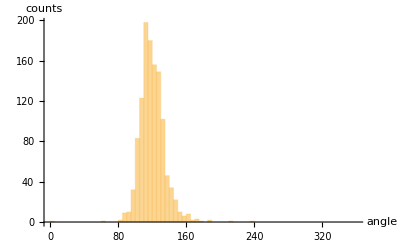

```mathematica
Histogram[{
Flatten[angles32,1]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[angles32,1]]
```

120.

```mathematica
StandardDeviation[Flatten[angles32,1]]
```

14.8939

#### FitList

```mathematica
vertex3MeasurementsRaw2
```

{{660.49,985.512,-1.66964,0.583269,2.43171},{433.5,983.486,-3.10022,-0.831829,0.918796},{64.5116,982.529,-1.02872,1.08767,3.00226},{853.499,982.499,-2.68411,-0.402904,1.83676},{726.491,975.502,-2.70214,-0.618706,1.61805},{234.491,974.505,-1.67579,0.468099,2.48792},{578.507,972.513,-1.40627,0.738619,2.59271},{938.508,972.479,-0.893203,0.958077,2.8865},{890.398,970.819,-0.924319,1.06435,2.97943},{496.523,969.499,-2.77371,-0.709434,1.46777},{744.49,962.525,-1.68564,0.256211,2.52303},{798.483,959.516,-2.09126,0.0290083,2.27448},{814.501,959.49,-1.07865,0.748967,3.04308},{456.495,958.513,-2.04091,0.143697,2.25813},{659.492,955.498,-2.52357,-0.325926,1.61575},{84.4978,950.507,-2.14332,0.119445,2.20763},{383.528,950.493,-2.81083,-0.909922,1.10304},{681.726,949.179,-0.893363,1.03651,2.90277},{520.498,945.493,-1.93322,0.0233072,2.30581},{363.498,942.522,-1.63323,0.390475,2.5678},{966.5,938.51,-2.02129,0.201317,2.29284},{317.521,936.503,-2.59659,-0.918344,1.70238},{397.49,933.508,-1.7249,0.35199,2.21388},{743.213,930.286,-1.72127,-0.155598,1.66487},{627.496,927.508,-0.971492,0.814506,2.67997},{918.507,927.506,-2.67049,-0.722395,1.55419},{783.198,925.952,-1.15603,1.09043,3.11743},{866.494,919.511,-1.72814,0.179976,2.43159},{898.499,916.504,-1.39254,0.510939,2.75794},{285.507,915.497,-1.33504,0.595196,2.42677},{739.91,906.48,-2.16669,-0.408247,1.48136},{647.485,904.51,-1.83039,0.0820364,2.39505},{517.502,900.515,-2.68851,-0.351368,1.80811},{108.485,898.513,-2.61888,-0.372541,1.74471},{221.5,898.485,-2.52579,-0.478223,1.71402},{395.508,898.5,-2.73205,-0.660831,1.54776},{290.498,896.506,-2.42008,-0.329978,1.85189},{859.515,895.5,-2.36562,-0.621719,1.19067},{11.4901,893.493,-2.51011,-0.114658,1.7536},{943.499,892.505,-2.4453,-0.108905,2.02786},{80.5062,886.508,-1.7701,0.279008,2.58071},{198.505,885.499,-2.87363,-1.1874,0.420627},{545.531,884.967,-1.84838,0.21794,2.43399},{642.505,881.498,-2.44983,-0.430239,1.43124},{774.488,876.503,-2.06188,0.443294,2.11799},{720.516,874.491,-3.12417,-0.968321,0.992388},{883.483,870.488,-2.23247,-0.141121,2.16019},{986.727,868.389,-3.08334,-1.2012,0.584096},{208.491,861.518,-2.17521,-0.275512,1.98795},{305.515,854.513,-2.85881,-0.658817,1.11513},{353.489,854.493,-2.3166,0.138045,2.00872},{607.174,856.07,-0.868731,0.677174,1.74614},{855.497,852.511,-2.12676,0.209845,2.19781},{746.51,847.498,-1.32383,0.622646,2.67694},{412.483,845.512,-2.07443,0.392629,2.36826},{518.503,844.505,-0.713472,0.936301,2.76962},{108.108,839.826,-2.91212,-1.08433,1.04518},{470.502,838.492,-3.01608,-0.87315,1.06819},{334.504,836.506,-1.18729,0.684855,2.67238},{1000.75,836.432,-2.83594,1.30115,1.33829},{695.496,832.494,-2.33586,0.0360535,2.16434},{843.505,832.494,-2.90764,-0.884274,1.06275},{543.503,826.506,-1.42564,0.643237,2.60589},{402.496,824.502,-2.68924,-0.575724,1.16918},{71.5048,817.499,-1.24005,0.575511,2.91908},{120.495,817.497,-2.1972,-0.0520833,2.10964},{861.488,813.495,-1.91206,0.462234,2.37574},{644.518,812.504,-1.13655,0.957319,2.87229},{235.905,801.502,-3.12238,-1.10969,1.14887},{29.5108,800.51,-1.4081,0.659988,2.58016},{808.508,799.497,-2.99191,-0.948623,0.895283},{204.864,795.577,-2.18288,0.464404,2.24821},{781.485,794.517,-2.08293,0.18801,2.30791},{495.5,793.484,-2.29394,-0.347233,1.86084},{722.512,791.494,-0.881675,0.988553,3.12864},{197.765,786.154,-2.96745,-1.06408,0.718293},{924.519,784.497,-1.46464,0.588622,2.51845},{176.497,780.507,-1.97789,0.343046,2.32108},{118.494,775.498,-2.14508,-0.17878,2.14088},{682.523,774.52,-1.44917,0.82069,2.68794},{276.479,773.472,-1.18704,0.320465,2.12554},{477.526,773.506,-1.01331,0.849509,3.08526},{823.502,768.5,-2.65671,-0.146813,1.84355},{851.503,768.497,-2.99623,-0.613594,1.31322},{545.5,762.491,-2.53328,-0.356957,1.52862},{280.485,761.506,-2.53356,-0.550279,1.88419},{784.489,760.499,-1.78583,0.0854447,2.13325},{598.611,760.418,-1.75058,0.606676,2.64741},{151.5,758.507,-1.90796,0.281046,2.4299},{922.504,756.495,-2.70088,-0.648517,1.31914},{870.494,755.484,-0.515134,1.03246,2.5354},{493.5,750.507,-1.96785,0.106093,2.25153},{893.503,747.489,-1.5164,0.151325,2.97602},{61.4972,745.497,-2.97652,-0.772807,1.17732},{520.514,745.499,-1.48114,0.59631,2.69296},{942.516,743.494,-1.68473,0.896775,2.64193},{333.508,741.497,-2.55398,-0.392854,1.7644},{94.5068,733.518,-2.73531,-0.686501,1.19453},{485.505,733.503,-1.19247,1.13719,3.08709},{626.506,727.508,-0.951231,0.775267,2.95783},{81.4647,726.52,-1.68859,0.507551,2.38919},{807.515,725.502,-1.72555,0.419214,2.62853},{394.492,720.498,-2.46017,-0.162686,2.09183},{262.501,719.508,-1.73425,0.257971,2.44202},{744.496,719.498,-2.43197,-0.372997,2.05623},{848.5,716.497,-1.94096,-0.069848,2.24654},{637.495,712.498,-1.95054,0.105302,2.16837},{75.6614,709.386,-2.90927,-0.919764,1.04329},{18.1595,708.053,-2.70259,-0.856225,1.26347},{800.519,706.489,-3.13124,-0.975047,1.04865},{64.4776,705.533,-1.72223,0.464954,2.58251},{774.492,700.505,-1.87271,0.43156,2.27564},{357.202,700.105,-1.37055,0.510862,2.78838},{948.501,698.498,-2.37696,-0.315292,2.04914},{429.492,697.49,-2.63179,-0.49185,1.74387},{574.503,693.505,-1.25597,0.694936,2.44991},{909.513,691.509,-2.68279,-0.707722,1.3352},{455.502,687.512,-1.21907,0.565411,2.89048},{301.502,683.489,-1.98331,0.398302,2.3751},{934.367,680.563,-3.08445,-0.846763,1.00879},{851.128,679.517,-2.03561,-0.0598769,1.98912},{729.505,676.487,-2.60383,-0.0589829,1.77693},{766.081,675.673,-3.13642,-1.03688,1.21333},{392.51,665.509,-2.67862,-0.682538,1.38245},{264.486,661.5,-2.2377,-0.180078,1.755},{809.906,659.519,-2.97483,-0.942425,1.22746},{344.496,659.511,-2.45111,-0.530346,1.16408},{60.503,658.49,-2.73223,-0.85833,1.28748},{289.507,658.498,-1.00803,1.07618,3.10966},{457.521,657.502,-2.81185,-0.794833,1.34122},{197.471,654.507,-2.09533,0.234991,1.92148},{977.508,651.501,-1.99916,0.736899,2.61399},{36.5056,647.501,-1.53415,0.475424,2.27052},{368.505,647.513,-0.932237,0.825767,2.72685},{659.499,644.483,-2.25745,-0.21344,1.97889},{326.512,642.535,-3.06868,-0.912933,0.838408},{299.497,640.489,-2.31952,0.0630304,1.9961},{848.486,640.498,-2.25349,-0.212479,2.02733},{688.889,639.17,-1.41273,1.12149,3.00937},{919.495,638.518,-1.98908,0.206961,2.30019},{865.529,636.503,-1.30267,0.93412,2.92068},{727.481,632.502,-1.99706,0.267546,2.3751},{183.508,624.493,-2.80032,-0.713215,1.18154},{827.498,617.505,-1.2478,0.73574,2.68972},{131.491,616.487,-2.49338,-0.429922,1.73729},{966.488,615.496,-2.6683,-0.365064,1.56804},{222.512,614.504,-2.65743,-0.727305,1.26915},{74.469,612.503,-2.46311,-0.499832,1.63822},{602.495,609.492,-2.349,-0.0996813,2.09744},{343.485,606.49,-2.30649,0.00255407,1.99285},{404.894,606.164,-2.37543,-0.0677243,2.13948},{206.512,605.513,-1.4346,0.521123,2.47103},{30.908,605.3,-0.751575,1.21464,3.07252},{117.259,603.61,-2.92413,-0.988708,0.780698},{461.494,603.499,-2.25131,-0.190854,2.09826},{833.065,601.966,-2.13508,-0.23882,1.93609},{268.489,601.49,-2.48185,-0.472293,1.47283},{941.495,596.515,-0.84452,0.840573,2.87483},{40.881,595.959,-1.77808,0.312123,2.42088},{768.074,592.995,-1.38568,0.560464,2.66975},{879.505,591.472,-2.37531,-0.099856,1.86024},{899.536,590.691,-3.11013,-0.928686,1.14426},{686.515,589.495,-1.47646,0.482761,2.74089},{248.49,588.496,-1.79406,0.501133,2.35393},{769.503,582.419,-2.42489,-0.486117,1.73333},{866.508,580.489,-1.38381,0.649511,2.44524},{200.501,579.516,-1.15085,0.971898,3.09895},{360.53,577.499,-2.65833,-0.658183,1.43266},{639.516,577.503,-2.61661,-0.667499,1.10399},{981.512,576.511,-1.21441,0.842911,3.07644},{327.531,575.487,-2.56977,-0.698829,1.31026},{438.51,571.482,-2.89587,-0.898333,1.01279},{687.492,571.489,-2.57044,-0.471344,1.56345},{494.499,570.504,-2.46812,-0.364315,1.86105},{914.49,567.501,-2.00722,-0.197893,2.11785},{337.507,566.503,-1.56781,0.451506,2.38708},{417.501,566.509,-2.11334,0.186481,2.21794},{753.532,559.498,-3.11124,-1.26629,1.03935},{613.509,558.511,-0.965673,0.719466,2.81495},{55.5021,552.493,-2.63216,-0.878855,1.04482},{143.492,552.498,-1.81371,0.417675,2.34539},{560.502,551.513,-1.02235,0.738258,3.07218},{721.491,551.508,-1.7319,0.475435,2.47474},{543.51,550.517,-1.76746,0.183892,2.32322},{801.496,549.486,-2.29241,-0.164772,2.09626},{389.497,548.48,-2.1229,-0.0982547,2.13054},{404.53,546.531,-0.895997,0.959467,2.99535},{908.497,546.503,-2.46145,-0.318242,1.47351},{40.6599,543.827,-1.3153,0.582896,2.69399},{123.49,531.506,-2.02248,0.287749,2.28063},{633.494,530.486,-2.39206,0.0122123,2.17906},{376.508,529.508,-1.14724,0.964837,3.08309},{349.491,528.5,-1.80806,0.131914,2.14403},{575.495,528.52,-2.22348,0.221715,2.20079},{67.5193,527.511,-2.70712,-0.546194,1.74925},{833.524,523.489,-2.48953,-0.663784,1.28251},{47.4934,522.49,-2.31129,0.118198,1.93717},{679.501,520.499,-1.91559,0.26966,2.42139},{215.506,518.506,-2.67116,-0.823886,1.33745},{932.494,518.493,-2.45456,-0.049722,1.7125},{517.468,517.699,-1.60876,0.448953,2.69658},{344.504,511.501,-2.69867,-0.819824,1.27486},{973.507,511.501,-1.92678,0.411573,2.58191},{107.514,505.518,-1.14648,0.898387,2.85988},{262.507,503.468,-2.87802,-0.469603,1.45213},{13.4741,499.524,-1.87649,0.411669,2.56524},{234.505,497.505,-1.91618,0.156455,2.28023},{586.642,494.893,-1.39758,0.688581,2.61067},{421.502,493.492,-1.70716,0.627965,2.55548},{723.436,492.223,-3.1127,-1.32827,1.23232},{663.508,490.504,-1.36282,0.900447,2.68186},{948.504,482.5,-1.4184,0.581846,2.84676},{114.497,480.505,-2.5805,-0.612598,1.67789},{528.483,480.511,-2.2706,0.175246,2.16294},{372.488,478.486,-2.24503,-0.0474641,2.1577},{782.513,477.495,-2.56966,-0.743406,0.86421},{486.778,474.927,-2.52443,-0.6505,2.02959},{858.476,472.497,-1.90022,0.0397911,2.17599},{675.481,462.502,-2.0711,0.0800951,2.17037},{952.514,461.503,-2.49728,-0.490039,1.7824},{507.504,459.501,-1.55276,0.695805,2.5143},{302.527,458.499,-1.08929,1.02526,3.00493},{138.498,453.506,-2.59235,0.118409,2.09537},{559.516,447.501,-2.84619,-1.11775,1.79404},{411.499,441.489,-2.50512,-0.405098,1.58426},{709.679,439.821,-1.90245,0.534855,2.01002},{72.18,440.657,-0.934171,0.856789,3.09922},{765.063,439.032,-2.66555,-0.876587,1.68582},{387.506,434.486,-2.6273,-0.0603899,2.0125},{663.505,428.503,-2.70596,-0.612095,1.38454},{641.162,422.209,-2.53416,0.0805572,1.85664},{603.501,422.501,-2.47316,-0.495844,1.50278},{984.475,421.507,-1.83583,0.0893158,2.02331},{343.495,419.505,-2.09827,0.171266,2.27028},{568.505,418.49,-2.4946,-0.574389,1.72434},{781.496,415.502,-2.32841,0.161358,2.10398},{524.502,408.48,-3.12497,-0.647088,1.18248},{334.063,401.567,-1.7276,1.14683,2.84269},{978.344,397.545,-3.05282,-0.898199,1.32602},{502.386,397.577,-1.45285,0.946179,2.88178},{545.696,395.775,-1.27304,0.96257,2.72283},{101.509,392.497,-3.14,-0.96249,1.03473},{225.507,382.498,-3.14079,-0.969613,0.906657},{551.479,381.475,-2.27226,-0.0474674,1.98642},{626.599,378.614,-1.42781,0.463609,2.76142},{592.512,376.521,-1.50227,0.537862,2.78867},{747.509,375.503,-2.68949,-0.750781,1.12417},{909.505,374.498,-2.35602,-0.371282,1.80275},{821.54,373.492,-0.803275,0.937357,3.11759},{829.468,364.545,-2.12257,0.0317972,2.21583},{897.497,361.518,-2.9794,-0.971369,0.85528},{61.5336,360.48,-2.70272,-0.537194,1.31726},{505.488,360.507,-2.42495,-0.328892,1.62383},{764.51,358.501,-2.10606,-0.473475,2.32046},{652.734,354.747,-0.909615,1.06882,3.04555},{528.523,353.523,-1.14727,0.858616,2.88902},{73.8687,353.329,-1.37133,0.430932,2.6312},{240.482,349.486,-2.15514,-0.083569,1.93299},{288.846,346.324,-1.83098,1.1446,2.92573},{723.509,346.494,-2.51525,-0.509151,1.39151},{951.558,346.503,-1.69088,0.141405,2.50531},{976.551,347.524,-1.34968,0.747616,3.08968},{426.828,342.617,-2.17288,-0.179321,1.88525},{817.505,339.489,-2.91108,-0.85798,1.14038},{750.505,336.501,-1.08402,0.980908,2.94364},{802.496,334.509,-1.93588,0.35586,2.49701},{338.505,332.491,-2.54956,-0.617282,1.46624},{689.905,321.926,-1.19156,0.662256,2.58128},{273.506,318.499,-2.93418,-0.883419,0.910121},{793.501,312.514,-0.587797,1.16864,3.03995},{160.859,307.893,-2.32554,-0.525593,1.92619},{562.483,302.506,-2.45897,-0.441776,1.6579},{646.49,302.5,-2.45284,-0.574582,1.59439},{43.4989,301.5,-2.32877,0.134347,2.19757},{408.499,294.484,-2.88627,-0.589616,1.32325},{580.514,293.507,-1.13891,0.700533,2.66205},{706.479,290.001,-2.1223,0.20971,2.1495},{498.931,289.743,-1.77896,-0.0718086,2.74854},{843.519,286.515,-1.10867,0.876587,2.89717},{954.607,282.35,-2.80051,-0.321537,1.46573},{295.497,274.504,-2.64707,-0.573219,1.73905},{765.5,274.503,-1.51809,0.161575,2.39234},{244.494,272.487,-2.72804,-0.2928,1.64698},{365.149,273.692,-1.45047,0.521482,2.7782},{125.501,271.506,-1.05264,0.699536,2.66835},{593.503,265.504,-2.46279,-0.774833,2.0272},{908.511,263.508,-1.13742,0.629075,2.81697},{66.5029,259.509,-1.66543,0.88145,2.67878},{546.511,259.499,-2.53821,-0.877184,1.68298},{160.508,247.507,-1.21262,0.747024,2.9704},{558.5,245.503,-1.82575,0.290397,2.24703},{658.501,244.5,-3.01513,-0.842809,1.17546},{323.492,241.494,-2.41796,-0.325079,1.9332},{420.501,241.506,-1.57278,0.469506,2.51428},{609.634,240.79,-1.71809,-0.173616,1.97198},{783.497,239.51,-2.10567,0.124516,2.34546},{514.507,235.501,-1.5294,0.683321,2.68365},{211.505,234.499,-2.79024,-0.804437,1.05357},{811.502,232.51,-1.90507,0.0989098,2.55685},{901.513,231.512,-1.30297,0.852086,2.86462},{103.718,226.89,-1.97236,-0.155409,1.74784},{294.868,226.732,-2.124,0.223884,2.23049},{289.318,216.445,-2.76106,-0.892919,1.07168},{228.506,216.499,-1.70642,0.438424,2.30859},{373.494,214.494,-2.39133,-0.625632,1.86706},{603.512,213.503,-2.79152,-0.713417,1.25284},{944.909,210.752,-2.04747,-0.24555,1.6498},{552.22,206.363,-1.44404,0.0668666,1.5779},{183.506,197.507,-2.70073,-0.749018,1.31188},{707.501,197.477,-1.92964,-0.0368811,2.39232},{762.507,195.495,-0.971178,1.15919,3.13837},{853.521,194.486,-3.1263,-0.985727,0.982942},{395.503,193.508,-1.72159,0.0869899,2.24808},{436.496,193.49,-3.10707,-0.724773,1.77489},{307.483,191.508,-2.06477,0.156556,2.15999},{645.508,190.495,-2.96215,-0.726793,1.13841},{628.494,187.511,-2.24919,0.144041,2.24287},{508.499,183.504,-2.47573,-0.542308,1.48517},{237.492,181.498,-2.19685,0.0176609,2.12905},{96.4944,171.497,-1.48408,0.701318,2.54395},{394.485,168.504,-2.32684,-0.504435,1.64505},{612.508,168.526,-1.23708,0.866692,2.73085},{292.514,167.504,-0.929097,0.942684,2.94138},{473.499,164.513,-2.11842,0.215203,2.28498},{197.502,149.502,-2.5969,-0.488977,1.51613},{551.483,146.501,-2.06678,0.243046,1.99459},{339.5,145.49,-2.76893,-0.230697,1.65575},{460.995,145.64,-1.1656,0.963233,3.04921},{359.515,140.498,-1.3078,0.605851,2.9486},{810.498,137.494,-2.33661,-0.333113,1.70918},{427.499,135.507,-1.32676,0.698782,2.28117},{55.4715,134.475,-2.4408,-0.518866,1.64569},{647.697,135.764,-1.59995,0.640976,2.74034},{16.4891,133.503,-2.30751,-0.341953,1.72874},{159.504,128.511,-2.79033,-0.930043,0.739383},{43.5087,123.521,-1.47902,0.769741,2.7545},{920.503,121.502,-2.6545,-0.630007,1.6044},{235.637,119.368,-2.14454,-0.0490431,2.26106},{646.506,119.506,-2.72068,-0.788521,1.45885},{258.513,117.503,-0.998617,0.727221,3.04043},{958.498,110.484,-2.47174,-0.417401,1.73845},{587.508,106.521,-1.15697,0.834732,3.13731},{785.044,104.277,-1.13958,0.99319,3.08105},{750.502,103.504,-2.31207,0.140588,2.09933},{182.483,101.506,-2.00503,0.151492,2.34136},{315.66,101.861,-2.67857,-0.850866,1.86834},{694.506,96.4953,-2.61411,-0.783285,1.55156},{216.509,95.5212,-1.15107,0.798393,2.62829},{361.51,95.4972,-2.76887,-0.795933,1.24571},{86.4852,94.4821,-2.15314,-0.0907613,2.15993},{659.491,89.4979,-2.55059,-0.671856,1.64693},{737.495,89.5127,-1.27102,0.81797,3.03349},{791.491,89.5002,-2.15224,0.00253831,1.97315},{596.498,88.4961,-2.42369,-0.237578,2.02408},{25.6934,88.0213,-1.30062,0.58123,2.71608},{702.904,87.7566,-1.70205,0.185622,2.30621},{279.494,86.5052,-1.80581,0.330747,2.25668},{620.509,86.4972,-3.05451,-0.56011,1.26235},{507.516,85.5072,-1.69666,0.0583534,2.55295},{670.849,82.0281,-1.55337,0.702065,2.63982},{165.504,75.5097,-1.33568,0.808697,2.78838},{227.489,74.4953,-2.1667,-0.304035,2.13357},{71.4451,73.2535,-1.2829,0.796188,2.92373},{31.49,71.4874,-2.28333,-0.114469,1.98563},{375.515,70.5034,-2.50789,-0.507283,1.78479},{449.517,70.4987,-2.58559,-0.691278,1.7902},{832.54,70.4621,-3.06033,-0.824235,0.92471},{820.499,69.4943,-2.29245,0.0502162,2.23121},{563.487,68.4991,-2.24284,0.268516,1.99321},{74.5091,61.4874,-2.33629,-0.380515,1.80322},{272.519,61.4866,-2.91117,-0.791199,1.26338},{169.479,59.5006,-2.4589,-0.544925,1.79653},{969.519,55.5247,-1.35086,0.721826,2.88373},{788.482,52.5057,-2.26888,0.157858,1.9835},{283.483,49.4885,-2.31949,-0.541814,2.27274},{339.48,48.5007,-1.61292,0.479709,2.41424},{884.495,48.5027,-1.63817,0.326239,2.2735},{214.049,46.923,-2.87653,-0.696588,1.25536},{101.491,46.4806,-1.86987,-0.158994,2.54276},{550.487,45.5099,-2.29087,-0.580919,1.22837},{699.513,45.4998,-2.81979,-0.726524,1.22888},{423.512,42.4912,-2.91526,-0.675112,1.11965},{681.497,39.4973,-1.73618,0.284195,2.32755},{149.505,36.5012,-3.08521,-0.86414,0.991169},{764.396,31.9229,-2.64604,0.479096,2.05391},{519.501,28.4782,-2.27515,0.0386197,1.95251},{883.495,27.493,-2.37148,-0.36138,1.5598},{840.512,20.4905,-2.96259,-0.481872,1.2844},{98.4966,19.5041,-2.35671,-0.360608,1.64128},{470.504,19.4941,-2.80468,-0.763249,1.14561},{726.487,18.512,-2.01131,0.335236,2.35228},{944.522,15.4975,-2.80542,-0.793954,1.29016},{363.519,14.5095,-2.72839,-0.557123,1.30567},{350.053,9.35496,-1.6452,0.348913,2.04709}}

### Fit result

```mathematica
Show[
imgColor2,
Graphics[Join[{RGBColor[{255,255,255}/255],Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+15{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements,1],
{RGBColor[{0,0,0}/255],Thick},Circle[#,10]&/@quadrupleVertices2]]
]
```

## Vertices - Image 3

### Triple vertices

We define triple vertices as those branch points determined that are more than 10 pixels distant from other branch points (4-arm vertices are decomposed into two triple vertices in the network skeleton).

```mathematica
tripleVerticesRaw3=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@branchPointCoords3,0.]]}]/@branchPointCoords3,#[[-1]]>10&];
Length@tripleVerticesRaw3
```

887

So far, we got rid off 3-fold vertices that lie close by as we interpret those as 4-fold vertices that are decomposed in the skeleton network. However, there are also 4-fold vertices that remain as such in the skeleton network. We now identify those by counting the number of white pixels in the 3x3 neighborhood of a branch point. Triple vertices have 4 (one center + 3 arms), 4-fold vertices have 5 white pixels in this region .

```mathematica
tripleVertices3=Block[{
tvs=tripleVerticesRaw3,
branches=branchImPrun3,
verticesImg,
verticesMorph,
quadVerts
},
verticesImg=ImageMultiply[ImageReflect@Dilation[Image[Transpose@SparseArray[Thread[Round[(tvs[[All,1]]+0.5)]->1],{1000,1000}]],ConstantArray[1,{3,3}]],branches];
verticesMorph=MorphologicalComponents[verticesImg];
quadVerts=Keys@Select[ComponentMeasurements[verticesMorph,"Count"],Values[#]>4&];

If[Length[quadVerts]>0,
verticesMorph=Binarize@ColorNegate@Image@Clip[verticesMorph/.Thread[quadVerts->-1],{-1,0}];
quadVerts=ImageValuePositions[MorphologicalBranchPoints[verticesMorph],1];

Select[tvs,Min[Function[x,Norm[x-#[[1]]]]/@quadVerts]>0.1&],
tvs
]
];
```

```mathematica
Length@tripleVertices3
```

883

### 4-fold vertices

```mathematica
quadrupleVerticesRaw3=Complement[branchPointCoords3,tripleVertices3[[All,1]]];
quadrupleVertices3=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@quadrupleVerticesRaw3[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@quadrupleVerticesRaw3],I];
Length@quadrupleVertices3
```

79

```mathematica
vertices3=Join[tripleVertices3,quadrupleVertices3];
```

```mathematica
HighlightImage[branchIm3,{AbsolutePointSize[3],tripleVertices3,AbsolutePointSize[6],quadrupleVertices3}]
```

-Graphics-

## Analysis of triple vertices - Image 3

Experimental network data labeled by pixel positions

```mathematica
dataraw=ImageData[imgProj3[[1]]];
```

```mathematica
{dy,dx}=Dimensions@dataraw;
```

```mathematica
data=Table[{j-0.5,dy-i+0.5,dataraw[[i,j]]},{i,1,Dimensions[dataraw][[1]]},{j,1,Dimensions[dataraw][[2]]}];
```

### Analysis

The fit data for each vertex is taken as the data points within a 20 pixel large radius around the branch point. If a second branch point lies closer than 20 pixels, the radius is reduced to this distance.

```mathematica
vertex3Data=Table[{vertex[[1]],{#[[1]]-vertex[[1,1]],#[[2]]-vertex[[1,2]],#[[3]]}&/@Select[Flatten[data[[Max[1,Floor[dy-vertex[[1,2]]-25]];;Min[dy,Ceiling[dy-vertex[[1,2]]+25]],Max[1,Floor[vertex[[1,1]]-25]];;Min[dx,Ceiling[vertex[[1,1]]+25]]]],1],Norm[vertex[[1]]-#[[{1,2}]]]<Min[20,vertex[[2]]]&]},{vertex,tripleVertices3}];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[vertex3Data[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Disk[{0,0},1]]
],{i,1,Length@vertex3Data}]
```

Fit triple vertices and exclude those for which the fit does not converge.

```mathematica
vertex3MeasurementsRaw3=ParallelTable[measureData[data,3],{data,vertex3Data},Method->"FinestGrained"];
```

FindMinimum::regex: Reached the point {0.544369,17.5632,0.25,-1.63319,2.85}, which is outside the region {{-10.,-10.,-6.28319,-6.28319,-6.28319},{10.,10.,6.28319,6.28319,6.28319}}.

FindMinimum::regex: Reached the point {-10.5949,0.,-1.63319,1.85,-0.233185}, which is outside the region {{-10.,-10.,-6.28319,-6.28319,-6.28319},{10.,10.,6.28319,6.28319,6.28319}}.

FindMinimum::regex: Reached the point {-0.0500389,16.1803,1.45,2.25,0.05}, which is outside the region {{-10.,-10.,-6.28319,-6.28319,-6.28319},{10.,10.,6.28319,6.28319,6.28319}}.

FindMinimum::regex: Reached the point {16.1803,0.,0.05,-1.23319,0.65}, which is outside the region {{-10.,-10.,-6.28319,-6.28319,-6.28319},{10.,10.,6.28319,6.28319,6.28319}}.

FindMinimum::regex: Reached the point {16.1803,0.,0.05,-1.43319,0.65}, which is outside the region {{-10.,-10.,-6.28319,-6.28319,-6.28319},{10.,10.,6.28319,6.28319,6.28319}}.

FindMinimum::regex: Reached the point {16.1803,0.,0.65,0.05,-0.833185}, which is outside the region {{-10.,-10.,-6.28319,-6.28319,-6.28319},{10.,10.,6.28319,6.28319,6.28319}}.

FindMinimum::regex: Reached the point {10.6167,0.,0.05,-0.833185,3.05}, which is outside the region {{-10.,-10.,-6.28319,-6.28319,-6.28319},{10.,10.,6.28319,6.28319,6.28319}}.

FindMinimum::regex: Reached the point {-1.25534,16.1803,1.45,0.25,2.25}, which is outside the region {{-10.,-10.,-6.28319,-6.28319,-6.28319},{10.,10.,6.28319,6.28319,6.28319}}.

FindMinimum::regex: Reached the point {16.1803,0.,0.05,-0.833185,0.85}, which is outside the region {{-10.,-10.,-6.28319,-6.28319,-6.28319},{10.,10.,6.28319,6.28319,6.28319}}.

FindMinimum::regex: Reached the point {16.1803,0.,0.05,0.65,-1.43319}, which is outside the region {{-10.,-10.,-6.28319,-6.28319,-6.28319},{10.,10.,6.28319,6.28319,6.28319}}.

FindMinimum::regex: Reached the point {1.19315,16.1803,1.45,2.25,0.05}, which is outside the region {{-10.,-10.,-6.28319,-6.28319,-6.28319},{10.,10.,6.28319,6.28319,6.28319}}.

```mathematica
fittedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw3],ListQ[#[[2]]]&][[All,1]];
failedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw3],#[[2]]==I&][[All,1]];
vertex3Measurements=DeleteCases[vertex3MeasurementsRaw3,I];
Length[vertex3Data]
Length[vertex3Measurements]
```

0

867

```mathematica
failedVertices
```

{1,28,34,63,81,134,246,298,349,509,572,615,783,798,809,869}

```mathematica
Show[
ListDensityPlot[vertex3Data[[#,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Annulus[{0,0},{20,40}]]
]&/@failedVertices
```

{}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Manipulate[
Show[
ListDensityPlot[(vertex3Data[[fittedVertices]])[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Join[{Annulus[{0,0},{20,40}],
Disk[vertex3Measurements[[Floor@i,;;2]]-(tripleVertices[[fittedVertices]])[[Floor@i,1]],1]},
{Darker@Red,Thick},
Flatten[Function[p,Line[{{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]],{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]]+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]@vertex3Measurements[[Floor@i]],1]]]
],{i,1,Length@vertex3Measurements}]
```

```mathematica
angles33=(Join[#,{360-Total@#}]&@(180/Pi*Differences[#]))&/@(vertex3Measurements[[All,3;;]]);
```

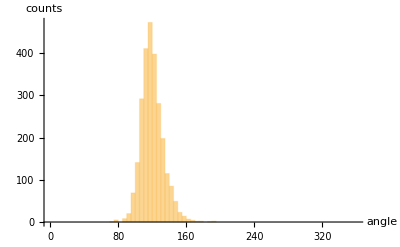

```mathematica
Histogram[{
Flatten[angles33,1]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[angles33,1]]
```

120.

```mathematica
StandardDeviation[Flatten[angles33,1]]
```

12.9531

#### FitList

```mathematica
vertex3MeasurementsRaw3
```

{ⅈ,{731.516,988.502,-2.09711,-0.537774,0.847679},{317.512,984.496,-1.89646,0.53755,2.25145},{548.495,980.522,-1.25648,0.8401,2.90731},{683.498,979.493,-2.5798,-0.585316,1.51469},{35.0529,979.198,-0.927402,1.07925,2.95749},{355.503,978.499,-1.51693,0.609576,2.57166},{124.494,977.499,-2.34805,-0.472516,1.93326},{940.291,976.88,-2.1685,0.329806,2.56267},{971.526,976.542,-0.719015,0.830192,2.8553},{775.494,975.492,-2.74179,-0.673736,1.03787},{387.508,974.508,-1.32498,0.554191,2.5624},{241.498,972.496,-2.59685,-0.619246,1.52044},{818.503,972.475,-2.4539,-0.0785128,1.88001},{838.619,970.407,-0.944217,0.891754,3.02256},{587.5,967.486,-2.56227,-0.538871,1.29235},{757.493,967.514,-1.83626,0.384769,2.3301},{209.508,966.499,-2.27365,-0.312736,1.75364},{66.5188,965.499,-3.11923,-1.05351,0.887561},{709.498,962.487,-1.78504,0.598177,2.54193},{884.49,962.495,-1.69666,0.417033,2.32456},{806.583,962.686,-1.4357,0.663724,2.92968},{554.505,960.494,-2.34616,-0.173728,1.81829},{577.519,959.517,-3.00511,-1.07653,0.777249},{479.501,957.531,-2.49007,-0.514481,1.96371},{501.415,957.178,-2.31626,-0.263207,1.66568},{924.487,957.505,-1.63512,0.772502,2.66941},ⅈ,{293.49,955.473,-2.24548,0.0476658,2.08147},{629.517,955.52,-0.941781,0.940395,2.89702},{199.358,955.285,-1.19762,0.791475,2.86095},{392.507,952.503,-2.44726,-0.432367,1.74453},{493.527,948.541,-1.3942,0.797167,2.48158},ⅈ,{657.505,946.495,-2.80307,-0.672765,1.31494},{880.508,945.484,-2.90309,-0.856367,1.2663},{414.505,942.508,-1.18311,0.759134,2.71506},{204.849,940.246,-2.28881,-0.154284,1.91604},{535.506,941.51,-1.11484,0.770562,2.67129},{639.486,941.505,-2.23,0.0866094,2.09534},{704.491,940.5,-2.68371,-0.448787,1.38346},{280.561,939.415,-1.10985,0.872276,2.84961},{813.471,937.488,-2.07779,-0.0517142,1.97212},{953.514,937.497,-2.81586,-0.741495,1.42208},{88.466,935.554,-1.68788,0.827293,2.50472},{330.503,933.508,-1.60932,0.520399,2.44782},{631.52,931.513,-2.7807,-0.888979,0.975525},{685.498,930.505,-1.61642,0.501058,2.6756},{741.508,930.499,-0.968062,0.939871,3.01774},{590.493,929.506,-2.17648,0.075781,2.05828},{490.536,926.494,-2.52803,-0.670516,1.19791},{896.5,926.513,-1.74552,0.176262,2.23879},{285.463,924.437,-2.85464,-1.20977,1.77998},{87.5067,923.489,-2.55303,-0.708249,1.55074},{779.507,923.478,-2.75975,-0.661243,1.43807},{138.509,922.523,-0.70399,0.811449,2.78483},{545.488,922.474,-2.27133,-0.419392,2.07683},{424.487,921.492,-2.37799,-0.0336252,2.1022},{858.49,921.505,-2.48592,-0.706318,1.61773},{805.074,919.696,-2.86037,-0.792667,1.28232},{187.501,918.506,-2.70528,-0.829207,0.935412},{237.494,918.492,-2.18907,0.0144446,2.1801},ⅈ,{49.4996,917.489,-2.17499,-0.0360159,2.03626},{642.489,915.505,-2.21358,-0.343031,2.10564},{101.524,914.531,-0.965469,0.715427,2.6072},{329.51,914.489,-2.51821,-0.545254,1.4687},{790.506,914.513,-1.78349,0.377477,2.47867},{70.5237,912.513,-1.51366,0.574953,2.80783},{371.503,908.506,-2.66244,-0.533914,1.31234},{532.509,907.509,-3.00308,-0.970046,0.882618},{161.496,905.503,-1.59041,0.513605,2.57323},{507.499,904.495,-2.63838,0.0940134,2.05001},{889.345,903.415,-1.47754,1.05156,2.87169},{291.487,902.483,-2.19624,-0.143628,1.79888},{591.29,901.193,-2.1405,-0.374214,2.03829},{308.506,899.497,-1.18381,0.638533,2.94896},{36.5073,898.499,-2.69732,-0.875189,0.987504},{351.486,897.506,-1.7007,0.506624,2.37748},{683.503,896.496,-2.36283,-0.384036,1.49726},ⅈ,{841.084,895.793,-3.00194,-0.988687,1.22557},{114.496,893.496,-2.14093,-0.00383348,2.07715},{393.507,893.499,-1.79115,0.52284,2.45874},{825.495,893.521,-2.08869,0.175457,2.1816},{212.497,892.491,-1.23743,0.633843,2.3793},{446.756,890.585,-2.11344,-0.23101,1.87742},{625.516,891.503,-0.816476,0.971938,2.71898},{889.506,890.5,-2.60242,-0.583391,1.51817},{724.518,887.497,-3.00812,-0.917443,0.915164},{965.767,886.274,-2.84946,-0.75108,1.47123},{280.504,885.494,-2.92558,-0.829191,1.0469},{544.489,885.495,-2.42273,-0.5527,1.95563},{929.213,884.944,-2.66571,-0.582219,1.39828},{160.087,884.077,-2.99425,-0.84782,1.43072},{710.522,883.54,-1.86294,0.311323,2.43789},{11.4741,883.246,-1.34846,0.641134,2.63818},{474.986,881.787,-1.50709,0.609421,2.64537},{666.497,880.498,-2.96363,-1.06731,0.71402},{937.334,878.643,-1.68126,0.34993,2.44787},{389.517,876.493,-2.7901,-0.807864,1.35014},{168.478,875.475,-2.26535,-0.120316,2.3337},{250.504,875.514,-1.40231,0.426582,3.0647},{559.524,875.53,-1.4751,0.485706,2.47004},{868.51,875.507,-1.36257,0.679801,2.72041},{907.691,877.123,-1.83789,0.321134,2.47956},{644.483,872.512,-1.78771,0.531977,2.39689},{475.481,870.487,-2.55505,-0.393041,1.64372},{99.5049,869.491,-3.02305,-0.919481,1.00213},{984.508,867.494,-1.8663,0.435179,2.32503},{434.495,866.512,-3.0748,-0.610874,1.16114},{770.487,865.491,-2.4199,-0.175407,1.98888},{787.105,863.861,-0.467027,1.32547,3.12529},{815.506,865.497,-2.61316,-0.580033,1.40289},{560.485,861.485,-2.48676,-0.507841,1.64274},{402.423,861.298,-1.5833,0.240412,2.20713},{701.504,859.503,-0.84382,1.16179,3.1275},{155.503,858.497,-0.827073,0.933349,3.13605},{733.512,858.483,-2.51023,-0.437946,1.4332},{449.497,855.495,-1.79177,0.453804,2.52235},{799.495,855.498,-1.39606,0.577763,2.48669},{21.5937,853.388,-1.9569,-0.0132397,2.00622},{110.382,853.667,-2.18033,0.153896,2.1215},{612.5,854.5,-2.35487,-0.285625,1.91726},{640.557,854.502,-2.6881,-0.623379,1.30457},{343.499,853.48,-2.38451,-0.404508,1.60148},{53.4966,850.513,-1.16146,0.838627,2.9664},{754.549,850.625,-1.38983,0.779561,2.88952},{252.515,848.475,-2.92608,-0.742077,1.47803},{629.522,848.493,-1.5004,0.523981,2.71839},{976.504,847.505,-2.70552,-0.802026,1.13297},{712.651,846.609,-2.05168,0.356288,2.23001},{314.487,844.503,-2.23294,0.102697,2.33876},ⅈ,{856.498,842.503,-1.64103,0.69713,2.71665},{590.5,839.484,-1.70587,0.440087,2.42239},{263.486,837.483,-2.09938,-0.173602,2.3449},{955.506,837.492,-1.89307,0.463508,2.32779},{513.502,835.495,-2.15255,-0.275917,2.4583},{706.074,833.966,-1.11787,1.05687,3.11444},{756.216,835.,-2.84103,-1.18219,1.60661},{14.5079,833.509,-2.71523,-0.692341,1.25716},{208.884,832.314,-3.00311,-0.555727,1.38446},{177.484,832.491,-2.20333,-0.0277939,2.19664},{670.499,830.52,-1.77487,0.241632,2.44957},{403.484,828.355,-2.60355,-0.515196,1.55155},{532.945,830.038,-1.29535,0.647875,2.87579},{301.507,826.512,-0.940616,0.978594,2.85571},{448.478,826.506,-2.66146,-0.407998,1.87649},{906.484,826.505,-2.2445,-0.409018,1.60154},{394.468,822.538,-1.79955,0.599545,2.44351},{100.502,821.493,-2.31475,-0.248331,1.45339},{167.521,820.525,-1.25631,0.848546,2.80559},{461.608,820.551,-1.41442,0.564164,2.69697},{851.52,819.496,-3.08561,-0.720866,1.19045},{586.506,818.491,-2.76021,-0.73673,1.34738},{800.497,818.507,-2.5819,-0.168856,1.51547},{946.241,817.033,-1.25836,1.02851,3.03668},{426.499,815.513,-1.66311,0.474602,2.56588},{632.494,813.488,-2.53099,-0.451139,1.70554},{667.513,813.596,-2.43191,-0.594448,1.43317},{70.5014,811.489,-2.31868,-0.254314,2.03775},{126.515,811.519,-1.23259,0.837144,2.66551},{827.536,811.531,-1.4355,0.567981,2.82016},{233.504,810.48,-2.23704,-0.0383358,2.26357},{248.678,809.724,-0.913671,1.00131,3.08129},{761.285,808.688,-2.47346,-0.33209,1.62811},{538.48,806.495,-2.39515,-0.571562,1.7429},{33.5041,804.49,-2.49316,-0.204744,1.85316},{351.484,803.499,-2.49263,-0.455659,1.6462},{498.516,803.494,-2.7224,-0.671234,1.28167},{779.507,801.514,-1.29046,0.80605,2.7365},{604.5,799.511,-1.98901,0.34184,2.25987},{312.495,797.495,-2.59487,-0.444764,1.70525},{552.627,798.289,-1.13366,0.747092,2.61522},{715.577,797.528,-3.06901,-1.01405,1.13851},{384.047,794.04,-1.04636,1.12968,3.05024},{176.498,792.498,-2.39133,-0.490936,1.87939},{260.493,792.503,-2.22726,-0.390035,2.16302},{475.997,793.376,-1.51095,0.43402,2.559},{956.792,792.783,-2.02817,0.124405,2.29115},{828.504,791.505,-2.63049,-0.56935,1.49749},{129.497,789.505,-2.43652,-0.420011,1.53063},{515.494,789.504,-1.70999,0.537675,2.45248},{10.0958,787.418,-1.0559,0.601599,3.01485},{210.498,787.501,-3.00343,-1.04896,0.696349},{721.746,787.452,-2.18684,-0.0256888,2.1102},{735.855,786.791,-1.16016,0.932007,3.06069},{782.495,785.504,-2.57309,-0.310502,1.62227},{893.493,783.492,-1.87773,0.0962093,2.15758},{951.717,783.18,-2.91305,-0.89737,1.09115},{284.502,779.501,-1.54765,0.613902,2.52707},{593.514,778.498,-1.14419,1.05708,3.13089},{937.495,778.495,-1.89926,0.376825,2.39476},{570.509,776.513,-1.93781,0.159391,2.48383},{158.521,775.525,-1.26701,0.791098,2.5766},{805.511,775.51,-1.1852,0.69592,2.66104},{513.51,774.518,-2.73557,-0.712828,1.42552},{853.525,773.52,-1.11334,0.734258,2.45254},{477.487,771.493,-2.58049,-0.2745,1.63039},{666.502,771.486,-2.31999,-0.165493,2.03591},{110.518,769.514,-1.28387,0.918322,3.03186},{709.511,769.5,-2.7335,-0.799095,0.989721},{81.4866,768.505,-1.91457,0.209598,2.19078},{767.495,765.498,-1.26955,1.21593,2.88017},{285.466,764.496,-2.42834,-0.433976,1.67421},{465.505,763.521,-1.59318,0.562703,2.50592},{698.172,764.181,-1.60277,0.525292,2.72797},{163.497,760.493,-2.35513,-0.401121,1.84021},{322.292,759.469,-3.04968,-0.9299,1.00318},{528.499,760.505,-2.13548,-0.117711,2.34478},{860.494,757.492,-2.29399,-0.0763907,1.90932},{885.168,758.057,-3.04567,-1.04114,1.23039},{393.522,754.494,-2.52457,-0.516673,1.42579},{806.53,753.487,-2.52436,-0.697182,1.40154},{928.517,753.505,-2.65397,-0.670281,1.20877},{552.522,752.506,-1.34187,0.597651,2.63161},{610.507,751.505,-1.90568,0.124213,2.29442},{75.0377,750.028,-2.94259,-0.87299,1.28244},{268.51,747.513,-1.1357,0.830267,3.02388},{774.5,747.495,-2.51797,-0.277144,2.01045},{462.517,746.512,-2.67922,-0.557953,1.29204},{115.504,744.006,-2.694,-0.570443,1.65129},{192.501,744.5,-2.01894,-0.201846,2.49107},{334.501,743.497,-2.12718,-0.00642063,2.21208},{847.502,743.521,-1.04482,0.810524,3.00975},{912.508,743.498,-3.12254,-1.17536,0.613691},{46.4905,742.512,-1.8716,0.333942,2.30764},{894.298,742.736,-1.8992,0.0927118,2.14575},{822.521,739.508,-1.82126,0.443425,2.4144},{215.511,737.515,-1.1659,0.842883,2.76996},{508.496,735.525,-2.72615,-0.930168,0.797061},{89.4725,734.509,-1.64979,0.251943,2.35998},{557.492,734.505,-2.27579,-0.155695,1.86271},{146.04,733.473,-1.23963,1.16867,3.05103},{275.493,731.493,-2.20571,-0.268631,1.9451},{602.518,731.501,-0.905165,1.08051,3.12639},{437.514,730.512,-1.36042,0.657166,2.51003},{588.497,729.533,-1.74648,0.188305,2.64306},{325.981,726.939,-2.44337,-0.464775,1.18329},{977.495,726.499,-0.832188,0.964702,2.88187},{487.501,725.498,-1.71825,0.533742,2.37982},{817.496,723.507,-2.73013,-0.853609,1.18149},{38.5164,719.487,-2.89219,-0.856152,1.20986},{89.4964,716.488,-2.53035,-0.626052,1.71229},ⅈ,{864.477,716.479,-2.27818,-0.11713,2.211},{226.499,713.501,-2.46514,-0.82196,2.04173},{884.594,714.486,-1.21517,1.15751,3.04997},{673.535,710.49,-0.946322,0.950254,3.11647},{721.504,708.5,-1.42609,0.606096,2.65156},{396.5,707.509,-1.99883,0.0880016,2.24855},{440.524,707.485,-2.43429,-0.351128,1.57255},{262.507,706.489,-2.73167,-0.643802,1.19865},{316.498,705.479,-2.44007,-0.573118,1.63737},{149.512,704.496,-2.61742,-0.706339,1.51662},{182.224,703.305,-2.54337,-0.353229,1.65897},{481.51,703.489,-2.94475,-0.594877,1.22003},{833.254,702.249,-2.29264,-0.215188,2.18581},{982.506,700.508,-2.57887,-0.713411,1.19239},{357.515,699.506,-2.46439,-0.36831,2.08707},{430.502,698.508,-1.17998,0.73336,2.76929},{241.495,697.496,-1.60312,0.396766,2.29051},{847.516,697.514,-1.3581,0.773971,2.77245},{771.49,696.508,-1.75007,0.358125,2.32277},{112.502,695.5,-2.2295,0.0737444,2.29025},{204.513,694.505,-1.51593,0.748629,2.73509},{617.504,692.496,-2.61139,-0.595077,1.86057},{894.501,692.499,-2.16424,-0.170415,2.05755},{164.509,691.511,-1.53041,0.549661,2.46164},{588.486,690.469,-2.43562,-0.627259,1.54662},{386.507,689.494,-0.872876,1.02009,2.84519},{335.786,685.808,-2.0456,0.437237,2.25072},{529.538,686.531,-0.943653,0.787329,3.13089},{510.469,683.514,-1.79292,0.288924,2.44557},{580.822,684.477,-1.40426,0.702088,2.6863},{935.524,683.494,-0.657841,1.18166,3.10562},{850.484,682.501,-2.29893,-0.322082,1.74237},{23.505,675.486,-2.34117,-0.192632,2.1678},{641.493,675.499,-1.81198,0.293944,2.48312},{89.5229,674.504,-1.35275,0.628253,2.78014},{947.527,673.549,-1.19888,0.765262,2.45415},{49.506,671.507,-0.952126,0.907792,3.05722},{443.485,671.488,-1.96905,0.0152178,2.12732},{507.525,671.512,-2.54053,0.0565716,1.32857},{768.496,668.501,-2.59427,-0.613208,1.55475},{162.314,665.349,-1.48658,1.34581,3.07195},{245.495,665.499,-2.16787,-0.210673,1.78999},{322.503,663.506,-0.886721,0.969307,2.90203},{494.493,662.505,-1.77461,0.580544,2.54206},{731.51,661.498,-2.29192,-0.345531,2.00884},{526.505,659.515,-0.971544,0.954581,2.5954},{950.803,660.098,-2.77118,-1.11611,1.63874},{639.474,657.481,-2.54089,-0.461796,1.60173},{588.503,656.499,-2.23219,0.00611576,1.99501},{281.511,655.526,-1.00491,0.79701,2.79232},{747.507,654.499,-1.80095,0.645179,2.6735},ⅈ,{794.587,652.284,-1.14572,0.945711,2.87115},{334.48,648.485,-2.05683,-0.116491,2.20106},{660.5,648.497,-1.49716,0.734437,2.79835},{956.978,646.099,-1.73806,0.128782,1.94824},{7.73579,646.814,-0.230503,1.42524,2.78461},{395.469,645.491,-2.17116,-0.254295,2.29799},{617.506,645.494,-2.17786,0.422046,2.36652},{349.526,644.506,-1.32528,0.626311,2.77175},{918.498,643.504,-1.76577,0.518673,2.5273},{438.482,641.499,-2.68096,-0.446715,1.59761},{800.486,641.499,-2.09843,-0.419249,2.11893},{576.497,640.514,-0.739733,0.928433,2.65254},{866.513,640.491,-2.93741,-0.935103,0.936825},{545.505,638.501,-1.63619,0.604492,2.44309},{822.351,636.965,-3.07228,-0.710728,1.19899},{421.496,633.499,-1.68337,0.406557,2.60861},{292.509,630.486,-2.51799,-0.203143,1.83532},{99.4943,629.494,-2.32981,-0.255633,1.92677},{120.514,628.497,-3.01411,-0.511625,1.40782},{831.519,628.526,-1.43977,0.556053,2.37543},{457.494,626.502,-2.06778,-0.0131129,2.26656},{476.496,626.492,-3.13813,-0.858149,0.994999},{597.906,627.238,-1.55477,0.527732,2.73114},{321.35,626.681,-1.11016,0.976187,3.09332},{166.491,623.484,-2.45777,-0.273771,1.86549},{542.514,621.488,-2.88282,-0.934416,1.32433},{790.426,622.422,-3.00405,-1.02755,1.11234},{912.894,619.319,-3.04501,-0.711872,1.30243},{741.505,619.492,-2.57919,-0.464206,1.47423},{989.528,619.515,-3.07758,-0.730989,0.633854},{180.526,618.536,-0.940259,0.776145,2.8329},{971.495,618.495,-1.98183,0.0365821,2.34437},{488.49,613.512,-1.93675,0.216579,2.32498},{597.504,611.492,-2.55719,-0.592158,1.514},{756.506,610.513,-1.33157,0.564396,2.5769},{27.5037,609.493,-2.76312,-0.856577,0.80296},{146.491,609.501,-1.88735,0.578258,2.41128},{719.504,608.494,-2.00988,0.394713,2.28828},{222.499,606.49,-2.52837,-0.57468,1.51604},{80.4959,604.505,-0.873242,0.964775,2.93932},{14.659,604.668,-1.81676,0.323484,2.48594},{191.49,602.487,-2.21627,-0.266349,2.1329},{616.502,602.497,-0.966787,0.720754,2.77283},{835.501,600.494,-2.58654,-0.517561,1.70977},{962.51,600.505,-2.88735,-0.598236,1.1111},{659.514,599.513,-2.65196,-0.644072,1.46895},{929.98,601.01,-1.92913,-0.258831,2.18976},{274.5,598.505,-2.47923,-0.706067,1.65842},{330.493,597.492,-2.42164,-0.284156,1.71774},{208.509,596.506,-1.45837,0.562604,2.77958},ⅈ,{353.497,595.47,-3.06214,-0.640998,1.17991},{481.5,595.49,-2.34396,-0.64127,1.24197},{139.51,591.513,-2.99492,-0.695475,1.18247},{384.455,591.477,-2.42598,-0.546752,1.57358},{579.511,591.488,-3.007,-0.741337,1.03331},{669.47,591.519,-1.6826,0.447161,2.45284},{850.505,591.515,-1.75909,0.71863,2.62045},{261.513,589.507,-1.5626,0.517492,2.65781},{704.501,585.504,-1.34939,0.821143,2.69824},{113.491,584.512,-1.59778,0.381467,2.55438},{394.483,585.362,-1.17332,0.663721,2.61299},{632.485,584.497,-1.47747,0.535435,2.41151},{177.51,583.514,-3.07665,-1.14096,0.950244},{371.495,580.512,-1.805,0.697344,2.40266},{437.497,580.487,-2.51765,-0.483903,1.34687},{924.5,579.504,-2.44343,-0.745059,1.47251},{152.438,580.135,-1.72094,0.247062,2.36257},{529.498,575.498,-3.06057,-1.39967,0.659085},{891.504,574.5,-2.34187,-0.367091,1.76909},{303.512,573.502,-1.34749,0.668482,2.54812},{510.512,572.516,-1.88962,0.28839,2.45489},{707.478,568.472,-2.53634,-0.444215,1.69141},{909.505,566.505,-1.60622,0.73544,2.7039},{149.552,564.724,-2.77387,-0.810432,1.32402},{406.481,565.518,-2.08762,0.291699,2.20437},{46.5105,563.504,-3.02473,-0.671383,1.1328},{721.506,562.498,-1.26449,0.57554,2.80255},{213.489,560.498,-2.28565,-0.550265,1.80457},{26.4963,559.515,-2.11399,0.219235,2.26816},{639.497,557.495,-2.59393,-0.262365,2.0426},{80.481,556.496,-2.47603,-0.432768,1.65532},{802.505,555.496,-2.77953,-0.830954,1.31836},{187.488,552.499,-2.3794,-0.271698,1.83866},{623.496,552.455,-2.35765,-0.126862,2.20112},{654.508,552.511,-1.49455,0.8003,2.72017},{499.508,551.506,-1.55718,0.912523,2.71745},{573.488,550.495,-2.20556,-0.358015,2.18322},{846.491,549.483,-2.28878,-0.43372,1.95332},{250.055,548.545,-1.05046,1.03697,3.03978},{309.505,548.477,-2.59878,-0.123389,1.80031},{201.516,547.525,-0.906111,0.808269,2.77089},{68.5153,546.51,-1.75571,0.67225,2.48494},{162.497,546.492,-2.29034,-0.312748,2.04735},{773.503,545.503,-1.75421,0.311267,2.27446},{943.488,545.478,-2.34997,-0.13056,1.82647},{395.523,544.502,-2.84289,-0.740595,1.13602},{956.674,544.114,-0.977599,1.01104,3.02877},{337.504,542.515,-1.18838,0.760249,2.82998},{175.513,541.507,-1.41618,0.739443,2.7644},{449.502,541.483,-0.764656,1.15132,3.03234},{866.5,540.508,-1.11323,0.84632,2.72823},{535.498,536.503,-2.46468,-0.276612,1.77536},{598.504,536.501,-1.78152,0.427288,2.44085},{726.309,535.679,-2.68775,-0.60043,1.63931},{257.5,535.505,-2.19121,-0.282778,2.08472},{406.496,533.494,-1.68675,0.394775,2.26576},{560.513,533.499,-3.11353,-0.892642,0.922969},{498.504,532.504,-2.66604,-0.598882,1.45966},{274.503,529.504,-1.36301,0.622409,2.78411},{690.495,528.495,-2.72065,-0.439057,1.49056},{768.513,527.499,-2.81689,-0.585206,1.26625},{344.295,525.025,-2.34151,-0.201472,1.95646},{665.482,525.484,-2.32488,-0.0682588,2.28819},{972.498,525.499,-1.65886,0.439717,2.35261},{464.488,524.481,-2.23239,-0.154004,2.16041},{357.502,522.507,-1.16403,0.756331,2.91011},{702.245,523.069,-1.41574,0.564182,2.75104},{878.505,522.504,-0.992896,0.625643,2.37211},{478.512,520.508,-1.2582,0.629594,2.78178},{517.501,520.512,-1.27144,0.757231,2.59941},{573.496,518.495,-2.02378,0.00814161,2.26387},{592.524,518.5,-0.760762,1.05178,3.11538},{54.4991,515.517,-1.26037,0.869777,2.73359},{125.483,514.512,-1.65336,0.391495,2.25937},{653.501,512.519,-1.21034,0.850672,2.8946},{217.49,511.486,-2.52008,-0.613776,1.96551},{601.483,509.49,-2.14203,-0.0936336,2.2697},{283.497,508.532,-1.96793,0.27433,2.22547},{887.486,508.479,-2.35498,-0.4912,2.12199},{412.5,507.519,-1.83935,0.176828,2.25542},{172.517,506.474,-2.47739,-0.542942,1.39938},{245.625,506.136,-2.75814,-0.770977,1.3712},{327.51,506.517,-1.35071,0.829102,2.72324},{918.499,506.496,-2.77975,-0.850817,1.50769},{615.522,504.515,-1.45204,0.715956,2.64961},{841.495,503.503,-2.59401,-0.566597,1.57892},{521.989,501.382,-2.02466,-0.151225,1.70787},{440.509,501.514,-1.67251,0.656417,2.57899},{232.485,500.521,-1.71617,0.44295,2.48306},{365.505,500.495,-2.12775,-0.320785,1.89611},{59.4931,499.496,-2.59701,-0.514457,1.83031},{707.49,497.507,-2.29159,-0.189862,1.87858},{196.504,495.514,-1.16762,0.664627,2.7979},{850.6,496.933,-1.80246,-0.06156,2.52261},{278.054,493.95,-2.86904,-0.579012,1.3052},{409.68,493.612,-2.84078,-0.471303,1.4193},{872.507,493.51,-0.960103,0.81583,2.9537},{558.514,492.509,-1.39053,0.962306,2.80961},{726.491,493.815,-1.28425,0.764681,2.92701},{969.483,492.492,-2.40812,-0.471468,1.58141},{663.5,491.498,-2.16182,-0.368591,2.06105},{930.498,490.501,-2.22495,-0.390877,2.14105},{262.486,488.51,-1.91035,0.355828,2.35703},{331.481,488.493,-2.45861,-0.490992,1.73221},{392.499,488.534,-1.79742,0.235402,2.56095},{124.492,487.494,-2.45039,-0.571411,1.59709},{41.5044,486.51,-1.40416,0.672547,2.78472},{80.4929,486.5,-0.72841,0.819269,2.56583},{157.521,481.501,-2.80907,-0.798512,1.28335},{772.499,479.498,-2.19669,0.0210956,2.21524},{690.496,478.504,-1.87163,0.811782,2.64335},{797.504,478.508,-1.2728,0.36928,3.05687},{954.51,478.515,-1.36668,0.728762,2.58309},{302.482,477.475,-2.00668,-0.0723819,2.42978},{620.5,476.511,-2.43875,-0.29355,1.79295},{143.494,475.515,-1.71195,0.426423,2.62514},{219.494,475.495,-0.909523,0.858657,2.94541},{316.486,476.065,-1.09992,0.740235,2.97256},{732.497,473.496,-2.30878,-0.381622,1.83716},{101.507,470.507,-1.9135,0.577851,2.60388},{387.512,469.493,-2.51076,-0.538884,1.30328},{513.514,468.503,-2.73178,-0.884951,1.37821},{648.735,469.095,-1.08706,0.932735,2.91078},{914.581,469.375,-1.31338,0.939506,3.12792},{888.488,467.506,-1.51858,0.157675,2.09624},{559.507,463.497,-2.57327,-0.562778,1.46692},{688.483,463.501,-2.35563,-0.492139,1.52462},{757.501,461.515,-1.76188,0.830079,2.61119},{256.504,459.488,-2.53897,-0.569495,1.48543},{602.509,457.503,-2.64698,-0.750236,0.954153},{654.49,457.514,-2.17522,-0.242985,2.04921},{409.495,456.509,-1.67345,0.521264,2.61298},{94.5022,454.489,-2.84303,-0.703876,1.11818},{176.502,453.486,-2.48371,0.00814988,2.03982},{329.491,453.473,-2.29641,-0.249376,2.15197},{714.502,453.523,-1.18873,0.861035,2.85055},{676.506,451.516,-1.19021,0.796474,2.85026},{591.502,450.51,-1.4729,0.623416,2.6746},{240.491,449.509,-2.25766,0.502624,2.2499},{488.511,449.523,-1.15065,0.846502,2.594},{847.013,448.227,-3.04778,-0.928132,1.32348},{276.503,448.493,-1.25661,0.596812,2.72217},{357.498,447.494,-1.29269,0.646349,2.97243},{958.492,447.482,-2.62401,-0.6048,1.54312},{457.526,444.506,-3.05172,-1.11053,0.919823},{106.494,443.507,-1.92315,0.0938912,2.37536},{818.77,444.226,-1.82644,0.272512,2.26313},{752.503,442.495,-2.65616,-0.674146,1.27744},{895.496,440.479,-2.09675,-0.11835,2.05907},{967.549,441.143,-1.54632,0.546717,2.47987},{212.486,435.504,-1.97038,0.0731949,2.29224},{229.279,436.276,-1.09556,0.891719,3.12725},{407.49,434.482,-2.67176,-0.571393,1.52224},{721.469,434.457,-2.45808,-0.502045,1.80966},{280.484,432.49,-2.33683,-0.333816,1.75443},{815.958,433.012,-2.78393,-0.684595,1.29738},{730.857,429.768,-1.39553,0.6532,2.68324},{417.591,428.738,-1.0855,0.646765,2.61299},{305.52,425.522,-1.05964,0.859807,2.92222},ⅈ,{686.488,422.494,-2.04021,-0.00333871,1.9277},{873.999,423.106,-2.00183,0.239342,2.48577},{465.502,421.493,-2.41726,-0.44514,1.80071},{46.4952,420.494,-3.05106,0.017924,1.69009},{785.494,420.515,-1.90448,0.314336,2.24572},{917.496,419.496,-2.41333,-0.334185,1.76},{102.488,418.486,-2.55281,-0.449537,1.59259},{636.506,418.503,-2.70936,-0.784628,1.34852},{424.487,416.448,-2.24273,-0.110344,2.14595},{973.226,414.098,-2.49184,-0.310373,1.88574},{312.49,413.472,-2.32988,-0.458574,2.04991},{496.259,411.489,-1.38916,0.750087,2.85036},{451.511,409.5,-1.478,0.68117,2.76915},{87.4958,408.503,-1.73422,0.543939,2.54285},{199.5,408.498,-3.0271,-0.865167,1.04309},{613.482,408.527,-2.04045,0.419547,2.38787},{902.505,407.487,-1.47175,0.622672,2.38199},{324.492,406.533,-1.68924,0.393778,2.62501},{779.501,405.495,-3.06983,-0.811262,1.13582},{962.905,405.431,-1.47614,0.702346,2.7009},{370.492,401.503,-2.47231,-0.431342,1.8701},{412.516,399.497,-2.81587,-0.911068,0.988091},{607.503,396.474,-2.81605,-0.807402,1.14983},{655.476,396.511,-2.23356,0.111,2.19491},{671.522,396.538,-0.873686,0.823181,3.00995},{787.003,397.441,-2.04917,-0.10391,2.28765},{739.593,396.152,-2.33811,0.261753,2.00861},{264.493,393.499,-2.14582,-0.306474,1.68804},{389.495,390.502,-1.73515,0.408812,2.55208},{217.501,389.507,-1.61835,0.485985,2.40414},{577.492,387.501,-1.69177,0.387883,2.55157},{730.498,387.508,-1.24538,0.729217,2.6636},{284.512,386.513,-1.34253,0.713967,2.81283},{680.447,386.508,-2.05505,0.156567,2.25695},{964.491,386.497,-2.18196,-0.395238,1.65894},{825.513,385.527,-1.90947,0.162662,2.62769},{31.8117,381.575,-1.95678,0.207593,2.43021},{79.6604,379.158,-2.72437,-0.562772,1.2163},{148.502,378.493,-2.7427,-0.666524,1.3053},{500.519,378.5,-2.80295,-0.900108,1.48398},{630.503,374.506,-1.49616,0.560785,2.46384},{66.5031,373.523,-1.87869,0.399085,2.36545},{458.488,373.484,-2.1211,-0.0788097,1.91872},{908.502,372.472,-2.88186,-0.0931713,1.7831},{253.504,370.511,-2.69347,-0.576827,1.27406},{575.504,369.509,-2.44911,-0.508298,1.45838},{322.49,367.495,-2.63123,-0.607461,1.75434},{387.481,366.501,-2.15906,-0.456341,1.62093},{165.49,365.506,-1.754,0.517741,2.50464},{289.648,363.178,-2.62734,-0.316186,1.78177},{510.498,364.498,-2.36962,-0.614756,2.08618},{946.5,364.522,-1.01727,0.825064,2.70712},{238.504,362.518,-1.63831,0.519394,2.6053},{548.806,362.619,-2.46308,-0.423262,1.94153},{678.492,361.489,-2.50189,-0.410343,1.7213},{729.511,361.484,-2.53426,-0.698598,1.23502},{117.513,360.508,-1.13426,0.658542,2.70366},{399.501,359.488,-1.84473,-0.0354332,2.57118},{420.519,359.492,-3.12317,-0.747296,1.11797},{780.507,358.485,-2.87047,-0.817055,1.43344},{304.501,357.501,-1.4701,0.483316,2.73233},{336.627,357.563,-1.64339,0.67946,2.57098},ⅈ,{272.484,355.525,-1.84219,0.35521,2.40353},{448.726,352.913,-2.7467,-0.677823,1.26503},{17.5248,352.499,-1.39125,1.01028,2.86661},{817.503,352.489,-2.92462,-0.584457,1.50896},{600.501,351.492,-2.1155,-0.323383,2.39995},{162.51,349.489,-2.60955,-0.672232,1.39266},{529.505,348.502,-1.31174,0.60151,2.36003},{744.487,348.505,-1.78985,0.333104,2.44757},{711.555,347.942,-1.95565,0.690255,2.74337},{124.468,346.495,-2.3399,-0.0694762,2.01578},{434.505,346.496,-1.51019,0.433858,2.36416},{658.503,345.535,-3.12285,-1.20137,0.696235},{792.494,345.505,-1.86249,0.314841,2.33734},{958.495,344.496,-2.39376,-0.0210033,2.16379},{202.514,343.496,-3.13109,-0.975463,1.01156},{369.5,343.511,-3.03141,-1.05829,0.828213},{830.564,343.708,-1.47051,0.681385,2.52814},{984.515,343.511,-1.03348,0.826175,3.11051},{176.499,338.501,-1.68702,0.401207,2.50393},{116.51,336.493,-2.95901,-0.97249,1.00194},{344.504,336.518,-1.67645,0.4328,2.40049},{948.675,335.841,-1.25122,0.738067,3.02051},{19.8721,333.185,-2.53256,-0.408675,1.60577},{61.5214,333.484,-2.52076,-0.686654,1.44825},{895.503,332.503,-2.42682,-0.515677,1.82896},{831.493,329.491,-2.42847,-0.393642,1.71177},{212.504,327.495,-2.174,0.0328728,2.04739},{231.162,328.066,-3.1062,-1.01601,1.11167},{309.5,327.504,-2.47467,-0.539603,1.83643},{536.508,326.492,-2.42433,-0.289366,1.94138},{589.498,326.503,-2.46277,-0.576706,1.28518},{698.504,321.511,-2.79956,-0.617853,1.07647},{44.5059,321.513,-1.56058,0.561269,2.65656},{912.495,321.499,-1.27026,0.652513,2.55355},{555.506,319.502,-0.947354,0.869082,2.75225},{270.482,318.476,-2.45155,-0.486788,1.76549},{744.494,317.5,-2.41952,-0.207296,1.86877},{86.5094,316.498,-1.37768,0.584922,2.63823},{525.522,316.527,-1.19915,0.744544,2.71758},{622.527,316.498,-3.13284,-1.1287,1.14954},{683.498,315.516,-1.73111,0.42854,2.59942},{438.475,314.479,-2.5258,-0.518002,1.71594},ⅈ,{335.51,311.51,-1.62206,0.935704,2.60016},{486.5,311.519,-1.29973,0.701369,2.88947},{175.479,310.491,-2.66882,-0.397003,1.6207},{379.488,310.494,-2.21832,-0.432384,1.73705},{876.504,310.496,-2.61827,-0.644044,1.03934},{244.493,309.512,-2.17643,0.123087,2.23407},{810.512,309.508,-1.21792,0.760374,2.98477},{450.513,306.521,-1.42668,0.507049,2.5286},{567.559,307.262,-1.02091,0.752486,2.45465},{958.498,304.489,-2.38777,-0.235743,1.91184},{191.502,303.507,-1.19882,0.737697,2.78224},{861.501,301.507,-1.30121,0.534937,2.31421},{146.604,301.489,-1.70216,0.309708,2.25771},{978.883,300.431,-1.16203,1.02494,2.96566},{417.085,297.97,-0.981681,0.780027,3.09491},{333.527,296.511,-2.74902,-0.651116,1.36698},{629.475,294.494,-2.61448,-0.746578,1.71029},{47.1888,292.889,-2.48301,-0.885099,1.74751},{94.497,293.498,-1.9912,0.00503702,2.02052},{785.49,290.499,-2.46566,-0.393826,1.50758},{815.503,290.509,-2.68017,-0.522992,1.70498},{926.107,291.134,-2.09338,0.0394822,2.15628},{144.923,289.497,-2.73169,-0.661217,1.40188},{671.533,289.506,-1.09653,0.945304,3.09086},{983.904,289.405,-2.21891,-0.396483,2.03487},{579.492,287.493,-2.09527,0.0499483,2.12012},{364.489,286.497,-3.08091,-0.857772,1.12837},{348.498,284.517,-1.72718,0.191452,2.42614},{493.494,283.499,-2.47044,-0.585576,1.77523},{641.487,283.517,-1.70192,0.503401,2.42727},{130.495,282.497,-1.8994,0.476334,2.54654},{608.507,282.514,-1.5792,0.525818,2.71154},{11.4804,280.498,-2.39939,-0.00430602,2.07666},{768.542,277.515,-1.48347,0.570758,2.53955},{679.494,272.495,-2.17252,-0.475709,1.91686},{532.378,267.119,-2.73471,-0.329241,1.47993},{722.653,267.422,-2.5484,-0.506001,1.61846},{462.711,267.566,-1.72719,0.279748,2.0935},{568.496,267.496,-2.99067,-0.814521,1.10758},{768.513,266.475,-2.40079,-0.540067,1.49563},{873.493,262.483,-2.25008,-0.450339,1.82153},{520.748,262.726,-1.845,0.409364,2.2052},{832.51,261.491,-2.71565,-0.910893,1.12833},{124.494,260.488,-2.93146,-0.556819,1.34961},{962.506,258.484,-2.91408,-0.85618,0.98981},{241.495,257.507,-1.27868,0.529936,2.42172},{887.502,255.513,-1.3991,0.732599,2.66966},{755.503,253.505,-1.25456,0.780306,2.80261},{639.99,252.082,-2.55037,-0.589133,1.52837},{941.502,252.514,-2.21049,0.318154,2.19266},{517.098,251.258,-2.91571,-0.831013,1.17348},{306.384,250.866,-2.46165,-0.71687,2.15207},{428.497,247.488,-2.52985,-0.379339,1.56727},{671.463,247.475,-2.53169,-0.53038,1.72748},{92.5254,246.505,-1.27584,0.604084,2.63916},{808.51,246.505,-1.39042,0.698042,2.84529},{329.509,242.496,-0.662995,1.1069,3.11017},{856.516,242.522,-1.21927,0.86658,2.71746},{205.506,241.511,-1.98376,0.855123,2.57711},{681.994,241.459,-1.49597,0.349688,2.65004},{982.498,240.499,-1.43736,0.708232,2.53305},{660.486,239.52,-1.66618,0.581589,2.63975},{291.511,238.516,-1.11768,0.699241,3.0657},{159.498,234.5,-2.32099,-0.376177,2.12999},{481.682,235.551,-1.31981,0.571949,2.75623},{257.496,233.499,-1.83669,0.372769,2.3685},{25.5261,230.48,-3.07364,-0.856124,1.07136},{613.501,230.513,-1.22827,0.759429,2.79756},{347.488,229.502,-1.21399,0.53231,2.54058},{936.499,227.505,-2.45353,-0.328649,1.87432},{541.509,225.492,-2.28657,-0.034038,2.23536},{565.519,224.508,-1.09057,0.732633,3.08898},{658.521,224.511,-2.60943,-0.474385,1.43814},{759.484,223.491,-2.433,-0.357817,1.60869},{34.5046,219.484,-2.20298,-0.0984467,2.22899},{812.486,219.493,-2.39413,-0.354806,1.65367},{901.486,219.491,-2.18412,-0.0618798,2.15518},{48.5115,218.482,-1.27598,1.03062,3.1053},{727.503,217.494,-1.95657,-0.239609,2.0696},{250.517,216.506,-1.1914,1.13317,3.05349},{98.7033,214.104,-2.64399,-0.361225,1.65509},{676.805,216.306,-1.46202,1.00796,2.72401},{921.534,215.521,-1.2815,0.64837,2.82637},{746.499,212.504,-1.26972,0.709342,2.87972},{355.497,210.485,-2.27858,-0.126135,2.06837},{490.495,210.504,-2.33835,-0.0923914,1.98995},{846.513,210.498,-3.03608,-0.986439,0.779801},{374.515,208.503,-0.956849,0.91545,3.03007},{831.938,209.38,-1.95357,0.0421385,2.35261},{118.513,206.52,-0.989289,0.844938,2.79992},{572.497,204.49,-2.73582,-0.470919,1.71029},{305.501,203.505,-2.38564,-0.275035,1.97835},{516.518,202.512,-1.34863,0.632197,2.59076},{789.507,201.497,-1.57112,0.588226,2.43614},{257.245,196.887,-2.36498,-0.412323,1.81351},{677.501,197.49,-2.73448,-0.780616,1.50294},{417.45,196.06,-2.93167,-0.640497,1.29836},{716.512,194.501,-2.68128,-0.765192,1.04076},{594.503,193.513,-1.77983,0.333948,2.707},{128.483,192.479,-2.17692,-0.100281,2.1334},{334.513,191.505,-1.34323,0.588642,2.58767},{386.482,191.504,-2.08604,0.0709332,2.14551},{248.488,188.48,-3.01776,-1.25304,0.779048},{965.519,187.496,-0.973388,0.963985,3.10303},{520.505,186.5,-2.33362,-0.37843,1.83079},{688.487,186.503,-2.05394,0.0938327,2.3456},{934.497,186.504,-2.02494,0.0921054,2.19624},{701.617,186.634,-1.33602,0.586064,3.05558},{283.505,183.511,-1.38175,0.72024,2.54614},{546.507,181.483,-3.12979,-0.80895,1.02782},{633.497,181.512,-1.57662,0.341329,2.07026},{864.491,180.489,-2.14186,-0.0498772,2.15233},{877.528,180.486,-3.07253,-0.702251,1.05925},{337.492,175.461,-2.29581,-0.129128,1.70893},{118.3,175.214,-0.894041,1.09771,3.05072},{222.507,174.512,-1.18648,0.707771,2.72401},{374.531,173.499,-1.34546,0.967772,2.90622},{86.4995,172.507,-1.6774,0.172418,2.39732},{975.498,172.498,-2.17168,-0.320102,2.09112},{471.493,171.498,-2.64009,-0.525591,1.54099},{793.507,170.483,-2.47054,-0.344344,1.84319},{824.522,169.461,-2.43628,-0.582873,1.44179},{585.504,167.51,-3.0051,-0.55249,1.119},{924.508,167.499,-2.80188,-0.858972,1.07598},{125.475,166.502,-1.83772,0.225859,2.28235},{675.523,164.495,-1.104,0.967431,3.1238},{46.5033,163.496,-2.97805,-0.996674,1.27901},{456.497,163.5,-1.66201,0.44416,2.26726},{170.344,161.736,-1.08165,1.00647,3.02554},{564.494,162.547,-1.88239,0.385479,2.31952},{778.492,162.492,-2.11172,0.351436,2.37136},{326.497,161.506,-2.73499,-0.834983,0.929263},{504.533,161.204,-1.07943,1.15342,3.02285},{815.485,161.51,-1.64681,0.695473,2.69386},{896.494,161.503,-2.06898,0.0938446,2.31712},{633.493,160.513,-2.70127,-0.52411,1.57938},{840.506,158.504,-1.17864,0.502663,2.51974},{24.5153,156.531,-1.49995,0.39121,2.63423},{376.507,156.486,-2.58505,-0.495152,1.48289},{230.495,153.485,-2.51111,-0.49709,1.89561},{645.515,153.519,-1.11275,0.751691,2.63539},{122.521,152.492,-2.57047,-0.674104,1.40854},{560.592,152.497,-2.55534,-0.620248,1.17799},{616.518,151.517,-1.55354,0.600126,2.56166},{176.491,150.473,-2.22602,-0.0743897,2.07638},{255.47,150.484,-2.6345,-0.484304,1.61541},{389.55,149.397,-1.36108,0.54266,2.64325},{744.496,147.501,-2.4647,-0.24436,2.02977},{245.494,144.491,-1.66932,0.515397,2.53538},{887.585,144.25,-3.06431,-0.92367,1.09505},{848.484,143.494,-2.0459,-0.0203418,2.12086},{345.493,141.51,-1.90001,0.387625,2.34755},{763.504,141.503,-1.14677,0.881527,2.80071},{85.5191,140.483,-2.45405,-0.375215,1.53371},{211.084,140.72,-1.9386,0.540975,2.56865},{616.534,138.533,-2.60273,-0.553495,1.53816},{164.503,134.494,-3.06266,-1.02986,0.956777},{515.505,134.496,-2.31839,-0.243606,1.88703},{78.4908,134.459,-1.63458,0.739666,2.58921},{293.437,132.479,-2.13399,-0.153527,1.98766},{145.486,131.52,-2.07415,0.186217,2.32715},{937.504,128.499,-2.82848,-1.14735,1.67912},{802.508,127.493,-2.81024,-0.786053,0.988873},{580.723,125.648,-2.54252,0.0996225,1.97955},{537.918,126.788,-1.1587,0.745768,2.64054},{403.492,124.511,-2.04222,0.228815,2.33238},{901.49,124.479,-2.42769,-0.108705,2.1626},ⅈ,{840.51,123.494,-2.75596,-0.705968,1.30638},{679.527,122.503,-2.80906,-0.597787,1.27831},{773.497,122.493,-2.21065,-0.00780531,2.08082},{19.4932,119.502,-3.04107,-0.579981,1.33179},{665.015,119.357,-2.16599,0.0538019,2.1242},{199.509,118.499,-3.12886,-0.97119,0.957153},{175.485,117.501,-1.91901,0.0642602,2.12191},{541.458,115.73,-2.54217,-0.4648,1.81666},{490.49,114.507,-1.58767,0.532307,2.23196},{816.502,113.495,-1.90759,0.402566,2.35381},{77.9179,110.033,-2.76632,-0.702232,1.51498},{634.489,110.496,-2.16903,-0.0142535,2.02452},{658.327,109.864,-1.30384,0.891568,3.12316},{856.498,110.521,-1.88551,0.239699,2.48947},ⅈ,{883.511,109.506,-1.36202,0.654507,2.81207},{558.52,108.511,-1.09295,0.695074,2.73496},{975.501,108.482,-2.28203,-0.409127,1.91582},{737.5,107.507,-1.7956,0.0724067,2.37014},{760.5,106.492,-1.04538,0.891531,2.9621},{699.486,105.506,-1.98105,0.51794,2.37837},{266.502,104.505,-2.6452,-0.769102,1.07949},{63.5076,103.518,-1.567,0.468761,2.56591},{234.505,103.508,-2.7587,-0.671769,1.20128},{129.508,101.507,-2.70727,-0.726577,1.07175},ⅈ,{213.488,97.5045,-2.14846,0.160185,2.14483},{565.295,94.4362,-2.06202,-0.0980349,1.93604},{247.498,92.5036,-1.83616,0.660568,2.45219},{95.6031,91.6483,-1.99274,0.0153535,2.25995},{109.511,91.5008,-1.1704,0.513059,3.09488},{769.499,91.4936,-2.3382,-0.392082,2.07249},{330.498,86.1,-2.97987,-0.823073,1.2151},{446.503,86.4831,-2.90568,-0.456517,1.24874},{491.487,85.4925,-2.64617,-0.624359,1.65721},{888.508,85.5088,-2.48554,-0.52175,1.75232},{163.79,82.0164,-1.61464,1.01384,2.78768},{422.501,81.4985,-1.91905,0.147912,2.35976},{521.505,81.4806,-2.71463,-0.497961,1.50693},{372.493,79.5099,-1.25849,0.537917,3.06086},{691.521,79.5021,-2.53585,-0.656455,1.40659},{796.511,79.5248,-1.12461,0.880147,2.6841},{340.481,76.5059,-2.04467,0.151891,2.37742},{470.502,75.5095,-1.57151,0.399222,2.74939},{905.409,75.0514,-1.90647,0.490764,2.46874},{506.502,73.5198,-1.7001,0.472426,2.45278},{671.553,69.9944,-2.64948,0.280373,2.00732},{964.506,68.4997,-2.32801,-0.312131,2.08818},{193.503,65.4955,-2.74854,-0.908249,0.927241},{238.499,65.515,-2.73498,-0.725036,1.18575},{161.507,64.5005,-2.73774,-0.515738,1.39567},{724.506,64.5022,-2.77482,-0.447139,1.27953},{862.493,64.9181,-1.20502,0.724608,2.83163},{655.493,61.5026,-1.70709,0.48374,2.45911},{294.499,60.4885,-2.35485,-0.15134,2.07454},{710.497,60.5041,-2.14994,0.160929,2.24389},{814.511,58.5159,-1.35859,0.501556,2.56613},{74.5226,57.5138,-0.878501,0.867825,2.85671},{381.496,57.5017,-2.07209,-0.00808713,2.06159},{173.528,55.5204,-1.4291,0.591226,2.42132},{410.524,55.5033,-1.14811,1.03314,3.0438},{951.98,55.8402,-2.96512,-1.05377,0.778811},{933.499,52.5055,-1.86869,0.189552,2.23933},{254.5,51.5067,-2.03,-0.145882,2.44919},{610.2,50.6719,-1.24107,1.14822,3.06709},{23.1595,46.6916,-1.14422,0.839076,3.00264},{581.509,46.5216,-1.61709,0.377971,2.59277},{277.505,45.4935,-1.40308,0.610263,2.72194},{85.477,44.5151,-1.82756,0.260862,2.21798},{214.168,44.9808,-1.58302,0.889953,2.47656},{652.603,38.0665,-2.57428,-0.698998,1.45535},{818.499,35.5087,-2.30807,-0.163355,1.70025},{703.49,34.5003,-2.42746,-0.571491,1.55778},{29.4856,33.4747,-2.19852,-0.232906,2.00106},{420.483,33.4767,-2.28549,-0.0808161,2.03444},{440.796,33.2926,-3.08943,-0.830641,1.16065},{836.905,32.5826,-1.09256,0.302135,2.98906},{370.027,31.6272,-2.98038,-0.569548,1.24799},{925.504,30.4879,-2.94033,-0.637338,1.19882},{279.482,29.4854,-2.43219,-0.513541,1.67041},{358.492,29.529,-1.99152,0.195711,2.34565},{898.494,29.4681,-2.35605,-0.223086,1.84603},{169.196,25.6115,-1.47277,1.11041,2.81591},{379.516,24.5076,-1.85097,0.0575537,2.48834},{576.509,24.4965,-2.6049,-0.797431,1.17411},ⅈ,{668.497,23.4957,-1.87762,-0.0411094,2.3816},{631.499,22.5109,-1.67225,0.719894,2.47884},{891.231,22.5774,-1.15663,0.600508,2.91832},{409.506,21.5192,-1.20862,0.82484,2.89148},{452.496,20.5237,-1.87873,0.2512,2.3145},{687.504,20.508,-1.59479,0.704369,2.86078},{129.099,19.6081,-2.72975,-0.9649,1.69643},{80.4959,16.4749,-2.49446,-0.425098,1.47628},{489.819,18.2339,-1.70364,1.23882,2.78797},{949.503,15.5116,-1.02888,0.949765,2.68376},{220.492,12.479,-2.19066,-0.278141,1.96385},{21.2377,11.2357,-2.7059,-1.10202,1.45001},{245.776,8.09999,0.156207,1.52413,3.08034},{751.573,-2.77981,-0.065484,1.55181,3.1251}}

### Fit result

```mathematica
Show[
imgColor3,
Graphics[Join[{RGBColor[{255,255,255}/255],Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+15{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements,1],
{RGBColor[{0,0,0}/255],Thick},Circle[#,10]&/@quadrupleVertices3]]
]
```

## Combined

```mathematica
anglesComb=Join[angles3,angles32,angles33];
```

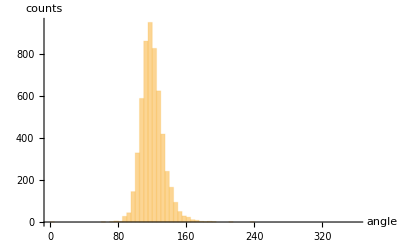

```mathematica
Histogram[{
Flatten[anglesComb,1]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[anglesComb,1]]
StandardDeviation[Flatten[anglesComb,1]]
```

120.

13.4435

## Domain statistics

## Image 1

Determine the domains alone:

```mathematica
domainIm=Pruning[Pruning@branchImPrun,Infinity]
```

-Graphics-

```mathematica
domains=MorphologicalComponents[ColorNegate@domainIm,"CornerNeighbors"->False];
```

```mathematica
domains//Colorize
```

-Graphics-

### Analyze domain-size and hole correlation

Length unit per pixel [µm]

```mathematica
dx=0.2125481;
```

```mathematica
domainMeas=SortBy[ComponentMeasurements[domains,{"Area","Holes"}],Values[#][[1]]&][[;;-2]];
```

```mathematica
domainInds=Keys@domainMeas;
```

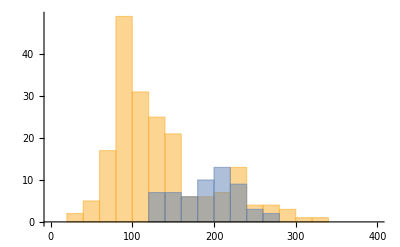

```mathematica
Histogram[{dx^2Select[Values@domainMeas,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeas,#[[2]]>=1&][[All,1]]},{0,400,20}]
```

### Number of corners of each domain

Have to take care of 4-fold vertices. In the branch network they fall apart into two triple vertices close by.
For some bubbles count two corners although above we would have classified it as a single 4-fold vertex.

```mathematica
Monitor[cornerNumber=Select[Table[Block[{
mask=Dilation[Image[Map[If[#==b,1,0]&,domains,{2}]],DiskMatrix[1]],
cornerCoords,
corners3,
corners4Raw,
corners4
},
cornerCoords=ImageValuePositions[ImageMultiply[branchPoints,mask],1];
corners3=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@cornerCoords,0.]]}]/@cornerCoords,#[[-1]]>10&];
corners4Raw=Complement[cornerCoords,corners3[[All,1]]];
corners4=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@corners4Raw[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@corners4Raw],I];
Length[corners3]+Length[corners4]
],
{b,domainInds}],#>0&];,b]
```

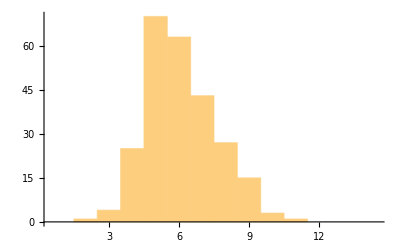

```mathematica
Histogram[cornerNumber,{0.5,15,1}]
```

```mathematica
N@Mean[cornerNumber]
```

6.13834

```mathematica
N@StandardDeviation[cornerNumber]
```

1.69049

## Image 2

Determine the domains alone:

```mathematica
domainIm2=Pruning[Pruning@branchImPrun2,Infinity];
```

```mathematica
domains2=MorphologicalComponents[ColorNegate@domainIm2,"CornerNeighbors"->False];
```

```mathematica
domains2//Colorize
```

-Graphics-

### Analyze domain-size and hole correlation

Length unit per pixel [µm]

```mathematica
dx=0.2125481;
```

```mathematica
domainMeas2=SortBy[ComponentMeasurements[domains2,{"Area","Holes"}],Values[#][[1]]&][[;;-2]];
```

```mathematica
domainInds2=Keys@domainMeas2;
```

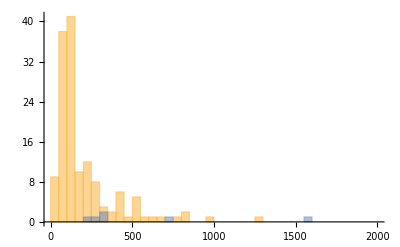

```mathematica
Histogram[{dx^2Select[Values@domainMeas2,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeas2,#[[2]]>=1&][[All,1]]},{0,2000,50}]
```

```mathematica
Histogram[{dx^2Select[Values@domainMeas2,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeas2,#[[2]]>=1&][[All,1]]},{0,2000,50}]
```

-Graphics-

### Number of corners of each domain

Have to take care of 4-fold vertices. In the branch network they fall apart into two triple vertices close by.
For some bubbles count two corners although above we would have classified it as a single 4-fold vertex.

```mathematica
Monitor[cornerNumber2=Select[Table[Block[{
mask=Dilation[Image[Map[If[#==b,1,0]&,domains2,{2}]],DiskMatrix[1]],
cornerCoords,
corners3,
corners4Raw,
corners4
},
cornerCoords=ImageValuePositions[ImageMultiply[branchPoints2,mask],1];
corners3=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@cornerCoords,0.]]}]/@cornerCoords,#[[-1]]>10&];
corners4Raw=Complement[cornerCoords,corners3[[All,1]]];
corners4=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@corners4Raw[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@corners4Raw],I];
Length[corners3]+Length[corners4]
],
{b,domainInds2}],#>0&];,b]
```

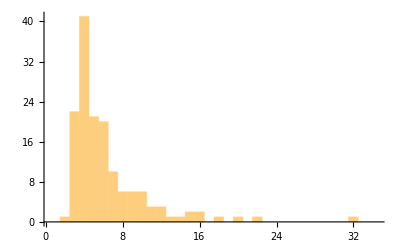

```mathematica
Histogram[cornerNumber2,{0.5,35,1}]
```

```mathematica
N@Mean[cornerNumber2]
```

6.30201

```mathematica
N@StandardDeviation[cornerNumber2]
```

4.10949

## Image 3

Determine the domains alone:

```mathematica
domainIm3=Pruning[Pruning@branchImPrun3,Infinity];
```

```mathematica
domains3=MorphologicalComponents[ColorNegate@domainIm3,"CornerNeighbors"->False];
```

```mathematica
domains3//Colorize
```

-Graphics-

### Analyze domain-size and hole correlation

Length unit per pixel [µm]

```mathematica
dx=0.2125481;
```

```mathematica
domainMeas3=SortBy[ComponentMeasurements[domains3,{"Area","Holes"}],Values[#][[1]]&][[;;-2]];
```

```mathematica
domainInds3=Keys@domainMeas3;
```

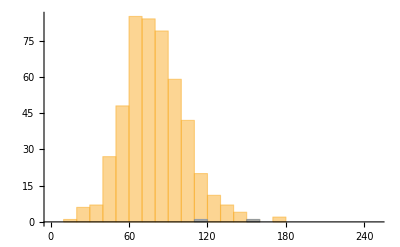

```mathematica
Histogram[{dx^2Select[Values@domainMeas3,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeas3,#[[2]]>=1&][[All,1]]},{0,250,10}]
```

### Number of corners of each domain

Have to take care of 4-fold vertices. In the branch network they fall apart into two triple vertices close by.
For some bubbles count two corners although above we would have classified it as a single 4-fold vertex.

```mathematica
Monitor[cornerNumber3=Select[Table[Block[{
mask=Dilation[Image[Map[If[#==b,1,0]&,domains3,{2}]],DiskMatrix[1]],
cornerCoords,
corners3,
corners4Raw,
corners4
},
cornerCoords=ImageValuePositions[ImageMultiply[branchPoints3,mask],1];
corners3=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@cornerCoords,0.]]}]/@cornerCoords,#[[-1]]>10&];
corners4Raw=Complement[cornerCoords,corners3[[All,1]]];
corners4=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@corners4Raw[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@corners4Raw],I];
Length[corners3]+Length[corners4]
],
{b,domainInds3}],#>0&];,b]
```

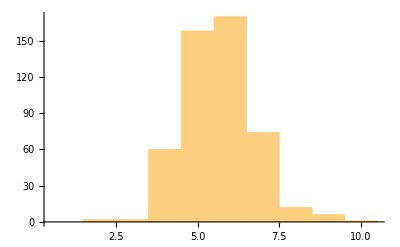

```mathematica
Histogram[cornerNumber3,{0.5,11,1}]
```

```mathematica
N@Mean[cornerNumber3]
```

5.64536

```mathematica
N@StandardDeviation[cornerNumber3]
```

1.09375

## Combined

```mathematica
domainMeasComb=Join[domainMeas,domainMeas2,domainMeas3];
cornerNumberComb=Join[cornerNumber,cornerNumber2,cornerNumber3];
```

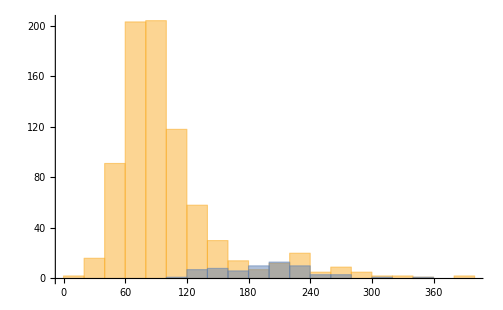

```mathematica
Histogram[{dx^2Select[Values@domainMeasComb,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeasComb,#[[2]]>=1&][[All,1]]},{0,400,20}]
```

```mathematica
Length@Select[dx^2Select[Values@domainMeasComb,#[[2]]==0&][[All,1]],#>400&]
Length@Select[dx^2Select[Values@domainMeasComb,#[[2]]>=1&][[All,1]],#>400&]
```

21

2

```mathematica
Mean/@{dx^2Values[domainMeasComb][[All,1]],dx^2Select[Values@domainMeasComb,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeasComb,#[[2]]>=1&][[All,1]]}
```

{121.931,113.667,226.438}

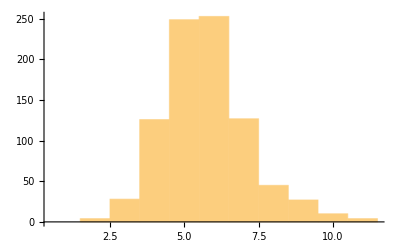

```mathematica
Histogram[cornerNumberComb,{0.5,12,1}]
```

```mathematica
Length@Select[cornerNumberComb,#>10&]
```

18

```mathematica
N@Mean[cornerNumberComb]
N@StandardDeviation[cornerNumberComb]
```

5.89628

2.08955